## Stability diagram plot

```mathematica
ClearAll["Global`*"];
```

### Defenitions

```mathematica
Clear[κ,α,Qp,Qm,γ,γd,γp,γa,a,μ];
Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ω=Sqrt[Qp/Qm] ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ]);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
(*M={{-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-Sqrt[(Qm/Qp)] (γp Cos[2 ψ]-γa Sin[2 ψ]),-γa Cos[2 ψ]-γp Sin[2 ψ],γp Cos[2 ψ]-γa Sin[2 ψ],Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-γp Cos[2 ψ]+γa Sin[2 ψ],-γa Cos[2 ψ]-γp Sin[2 ψ],Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-γa Cos[2 ψ]+γp Sin[2 ψ],γp Cos[2 ψ]+γa Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qp/Qm] (-γp Cos[2 ψ]-γa Sin[2 ψ]),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-γp Cos[2 ψ]-γa Sin[2 ψ],-γa Cos[2 ψ]+γp Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};*)
```

```mathematica
MR={{2(γa+I γp),0,2Sqrt[Q] (1+I α)κ},{0,2(γa-I γp),2Sqrt[Q] (1-I α)κ},{-γ/κ Sqrt[Q] (κ+γa),-γ/κ Sqrt[Q] (κ+γa),-(γd+2γ Q)}};
```

```mathematica
Coefs=CoefficientList[CharacteristicPolynomial[MR,λ],λ]*(-1)/.{Q-> 1/2(κ μ/(κ+γa)-1)}//FullSimplify;
```

#### Tests:

```mathematica
Coefs[[1]]
```

4 (γa^2 γd+γp (γd γp+(γ (-γp+α κ) (γa+κ-κμ))/(γa+κ))+(γ γa (α γp+κ) (γa+κ-κμ))/(γa+κ))

```mathematica
M.{0,Sqrt[Qp],0,Sqrt[Qm],0,0}//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&
```

{0,0,0,0,0,0}

```mathematica
M//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&//MatrixForm
```

(√(Qm/Qp) (√(1-a^2) γa+a γp) | √(Qm/Qp) (a γa-√(1-a^2) γp) | -√(1-a^2) γa-a γp | -a γa+√(1-a^2) γp | √Qp κ | √Qp κ
√(Qm/Qp) (-a γa+√(1-a^2) γp) | √(Qm/Qp) (√(1-a^2) γa+a γp) | a γa-√(1-a^2) γp | -√(1-a^2) γa-a γp | √Qp α κ | √Qp α κ
-√(1-a^2) γa+a γp | a γa+√(1-a^2) γp | √(Qp/Qm) (√(1-a^2) γa-a γp) | -√(Qp/Qm) (a γa+√(1-a^2) γp) | √Qm κ | -√Qm κ
-a γa-√(1-a^2) γp | -√(1-a^2) γa+a γp | √(Qp/Qm) (a γa+√(1-a^2) γp) | √(Qp/Qm) (√(1-a^2) γa-a γp) | √Qm α κ | -√Qm α κ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

### For gradient method

```mathematica
avars={a5,a4,a3,a2,a1};
vars={Qp,Qm,ψ};
params={Λ,γp};
charpolycoefs={-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((Sqrt[Qm^3 Qp]-Sqrt[Qm Qp^3]) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) Sqrt[Qm Qp] (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm Sqrt[Qm Qp] α γ γa Sin[4 ψ]+Qp Sqrt[Qm Qp] α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm Sqrt[Qm Qp] γd γp Sin[4 ψ]-Qp Sqrt[Qm Qp] γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+Sqrt[Qm Qp^5]) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((Sqrt[Qm^5 Qp]-3 Sqrt[Qm Qp^5]) γa-(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp Sqrt[Qm Qp] α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm Sqrt[Qm Qp] α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 Sqrt[Qm^3 Qp] γ γa+4 Sqrt[Qm Qp] γa γd+4 Sqrt[Qm^3 Qp] γa γd+4 Sqrt[Qm Qp^3] γa γd-Sqrt[Qm^5 Qp] γa κ+3 Sqrt[Qm Qp^5] γa κ+Sqrt[Qm^5 Qp] α γp κ+Sqrt[Qm Qp^5] α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 Sqrt[Qm Qp^3] γd γp+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((Sqrt[Qm Qp]+2 Sqrt[Qm^3 Qp]+Sqrt[Qm Qp^3]) γ+Sqrt[Qm Qp] γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+Sqrt[Qm Qp^3] γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
charpolycoefs=charpolycoefs[[1;;5]];
stateqns={
κ(Ns+ns - 1)-γa Sqrt[Qm/Qp] Cos[2 ψ]- γp Sqrt[Qm/Qp]Sin[2 ψ], κ  α(Ns+ns - 1)+γa Sqrt[Qm/Qp] Sin[2 ψ]-γp Sqrt[Qm/Qp]Cos[2 ψ]-ω,κ (Ns-ns- 1)-γa Sqrt[Qp/Qm]Cos[2 ψ]+ γp Sqrt[Qp/Qm] Sin[2 ψ],κ  α(Ns-ns - 1)-γa Sqrt[Qp/Qm]Sin[2 ψ]-γp Sqrt[Qp/Qm]Cos[2 ψ]-ω,-γ(Ns -Λ)-γ(Ns+ns) Qp-γ(Ns-ns) Qm,-γd ns-γ(Ns+ns) Qp+γ(Ns-ns) Qm};
stateqns[[2]]=stateqns[[2]]-stateqns[[4]]//FullSimplify;
stateqns=Drop[stateqns,{4}];
HwM={
{a1,a3,a5,0},
{1,a2,a4,0},
{0,a1,a3,a5},
{0,1,a2,a4}};
dDda=Table[D[Det[HwM],avars[[i]]],{i,1,5}];
dadx=Table[D[charpolycoefs[[i]],vars[[j]]],{i,1,5},{j,1,3}];
dadp=Table[D[charpolycoefs[[i]],params[[j]]],{i,1,5},{j,1,2}];
solNn = Solve[stateqns[[4;;5]]==0,vars[[4;;5]]][[1]]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns = stateqns[[1;;3]]/.solNn//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
dfdx=Table[D[stat3eqns[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dfdp=Table[D[stat3eqns[[i]],params[[j]]],{i,1,3},{j,1,2}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
```

Part::take: Cannot take positions 4 through 5 in {Qp,Qm,ψ}.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

### Solution

```mathematica
(*Solving stationary problem*)
	
γa=-0.01;
γ=1.;
γp=53.3669;
κ=300.;
γd=50.;
α=3.;
μ=5;
Qp0=0.9;
Qm0=0.1;
a0=0.205;

γa=0.1;
γ=1.;
κ=300.;
γd=50.;
α=5.;
γp=0.0382992;
μ=1.03482;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

Qm0v2=1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
Qp0v2=1/2 (-1+Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
tan0v2=((α γa-γp) Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2])/(2 γ (γa+α γp)^2 κ (-1+μ));
a0v2=tan0v2/Sqrt[1+tan0v2^2];
If[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2<0.3*(2 γ (γa+α γp) κ),Qm0v2=(μ-1)/2;Qp0v2=(μ-1)/2;a0v2=0;]
(*Qm0v2=(μ-1)/2*0.1;Qp0v2=(μ-1)/2*0.9;a0v2=0;*)
(*Nsol=NSolve[{Eq1==0,Eq2==0,Eq3==0},{Qp,Qm,a}]//Select[#,AllTrue[{Qp,Qm,a}/.#,#∈Reals&]&]&;*)
(*If[Length[Nsol]==0,Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}],
ElSol=Select[Nsol,(Abs[Qp-Qm]/.#)>10^-6&];
If[Length[ElSol]==0,Nsol=Nsol[[1]],Nsol=ElSol[[1]]]
];*)
(*β=((α γa-γp)-(γa+α γp) a0)/((α γa-γp) +(γa+α γp) a0);
Qp0=(μ-1)/(1+β);
Qm0=β Qp0;*)
Nsol2=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0v2,N[10^-8],10.},{Qm,Qm0v2,N[10^-8],10.},{a,a0v2,-1.,1.}}]
(*Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];*)
(*Ns-1/.Nsol
ns/.Nsol
Nsol*)
```

FindRoot::nlnum: The function value {Eq1,Eq2,Eq3} is not a list of numbers with dimensions {3} at {Qp,Qm,a} = {0.01741,0.01741,0.}.

FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0v2,N[1/10^8],10.},{Qm,Qm0v2,N[1/10^8],10.},{a,a0v2,-1.,1.}}]

```mathematica
1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ)
```

0.000625799

```mathematica
(2 γ (γa+α γp) κ)
```

704.767

```mathematica
Qp0v2
```

0.00328366

```mathematica
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0194168,0.000603856,1.}. Try perturbing the initial point(s).

{1,{Qp→0.0194168,Qm→0.000603856,a→1.}}

```mathematica
μ
```

1.03482

```mathematica
γp
```

0.0382992

```mathematica
Ns/.Nsol2
```

1.01291

```mathematica
ns/.Nsol2
```

0.

```mathematica
a0v2
```

-10.1996

```mathematica
{Eq1,Eq2,Eq3}/.Nsol2
```

{1.22208×10^-13,1.22208×10^-13,-5.39002×10^-18}

```mathematica
{Eq1,Eq2,Eq3}/.{Qp->0.019416770387043453,Qm->0.0006038557320213998,a->1.}
```

{4.23356,4.68643,-0.560016}

```mathematica
Qp0v2
```

0.

```mathematica
Sin[ArcTan[a/.Nsol]]
```

{-0.205778,-0.205778,0.205778,0.205778}

```mathematica
-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2
```

18.4195

```mathematica
{Qp0v2,Qm0v2}
```

{0.02096,0.02096}

```mathematica
(*Evaluating charpoly*)

p=CoefficientList[CharacteristicPolynomial[M/.Nsol2,λ],λ];
p[[1]]=0;
(*p=-CoefficientList[CharacteristicPolynomial[(tmp2/.Nsol),λ],λ];*)
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
If[AllTrue[p,NonNegative],
If[AllTrue[Dets,NonNegative],
Print["System is stable"];
Print[p//MatrixForm];
Print[Dets//MatrixForm],
Print["Some Hurwitz determinants are negative:"];
Print[p//MatrixForm];
Print[Dets//MatrixForm]
],
Print["Some p < 0"];
Print[p//MatrixForm];
Print[Dets//MatrixForm];
]
```

Some p < 0

(0
-202.126
4.87752
1018.02
72.7617
50.669
1)

(74067.8
-2.89319×10^8)

```mathematica
Nsol
```

{Qp→0.350028,Qm→0.350028,a→0}

```mathematica
If[Positive[-CharacteristicPolynomial[tmp2,λ]],If[AllTrue[Dets,Positive],Print["System is stable"];Print[p];Print[Dets],Print["Some Hurwitz determinants are negative:"];Print[p];Print[Dets]],Print["Some p < 0"];Print[p]]
```

If[Positive[-CharacteristicPolynomial[tmp2,λ]],If[AllTrue[Dets,Positive],Print[System is stable];Print[p];Print[Dets],Print[Some Hurwitz determinants are negative:];Print[p];Print[Dets]],Print[Some p < 0];Print[p]]

```mathematica
p
```

{1.91066×10^7,422612.,68199.,1328.33,52.4401,1}

```mathematica
({{3.232764872790355*^-8}, {1.910655999879378*^7}, {422611.74144311715}, {68199.01081752068}, {1328.32937396901}, {52.44011333711123}, {1}})({{52.44011333711123}, {1458.7321024281991}, {-6.073344503642392*^7}, {-4.313731141096*^12}, {-8.24205628660157*^19}}){Qp->0.3500283342778091,Qm->0.35002833427780905,a->-1.0848001355988288*^-16}
```

### Plotting by pixels v0

```mathematica
γa=-0.01;
γ=1.;
γp=10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
ysub={Sqrt[1-a^2]-> -Sqrt[1-a^2]};
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,5.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
result2=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];

Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result[[i,j]]=1,result[[i,j]]=0.7],
result[[i,j]]=0;
]
(*result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] ***=> D4 fails****)
,
result[[i,j]]=0;
];
Dets=ConstantArray[0,5];
HurwM={
{p[[6]],p[[4]],p[[2]],0,0},
{1,p[[5]],p[[3]],0,0},
{0,p[[6]],p[[4]],p[[2]],0},
{0,1,p[[5]],p[[3]],0},
{0,0,p[[6]],p[[4]],p[[2]]}};
Dets[[1]]=HurwM[[1,1]];
Dets[[2]]=Det[HurwM[[1;;2,1;;2]]];
Dets[[3]]=Det[HurwM[[1;;3,1;;3]]];
Dets[[4]]=Det[HurwM[[1;;4,1;;4]]];
Dets[[5]]=Det[HurwM[[1;;5,1;;5]]];
If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result2[[i,j]]=1,result2[[i,j]]=0.7],
result2[[i,j]]=0;
];
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.Nsol//Chop)==  0]],result[[i,j]]=-1]
]
];
Image[Reverse[result]]
Image[Reverse[result2]]
Image[Reverse[Abs[result2-result]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
Select[Abs[result2-result]//Flatten,#≠  0&]
```

{}

```mathematica
Select[result//Flatten,#==-1&]
```

{}

```mathematica
newres=Table[If[result[[i,j]]>0.5,1,0],{i,1,Nμ},{j,1,Nγp}];
contour=Abs[newres[[2;;,2;;]]-newres[[;;-2,2;;]]]+Abs[newres[[2;;,2;;]]-newres[[2;;,;;-2]]];
rgb=ConstantArray[0,{Nμ,Nγp,3}];
rgb[[;;,;;,2]]=newres;
rgb[[2;;,2;;,1]]=contour;
Image[Reverse[rgb]]
```

-Graphics-

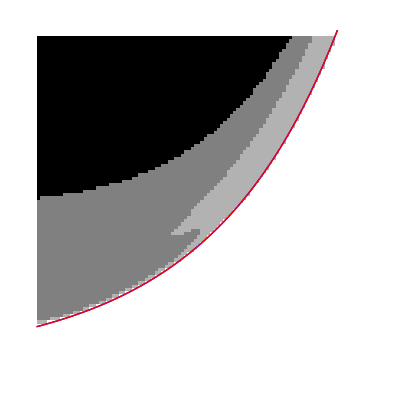

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuMine[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
Diff[γp_]:=(MuMine[γp]-Mu[γp])/MuMine[γp];

lp=Plot[(Mu[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];
lmp=Plot[(MuMine[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick}];
Show[ap,lmp,lp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

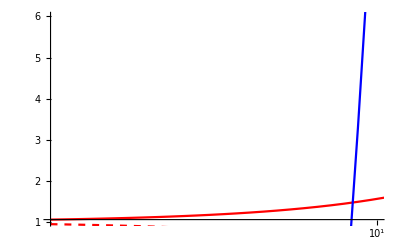

```mathematica
pl1 = Plot[1+γd*x/(γ (α κ - x)),{x,1,100},PlotStyle->Red,ScalingFunctions-> {"Log10",None}];
pl2 =Plot[1-γd/γ+2α x/γ,{x,1,100},PlotStyle->Blue,ScalingFunctions-> {"Log10",None}];
pl3 = Plot[1-γd*x/(γ (α κ + x)),{x,1,100},PlotStyle->{Red,Dashed},ScalingFunctions-> {"Log10",None}];
pl4 =Plot[1-γd/γ-2α x/γ,{x,1,100},PlotStyle->{Blue,Dashed},ScalingFunctions-> {"Log10",None}];
Show[pl1,pl2,pl3,pl4,PlotRange->{{0,1},{1,6}}]
```

```mathematica
oldresult=result;
```

### Plotting bound

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[κ,α,γ,γa,γp,γd,μ,Qp0,Qm0,a0,Eq1,Eq2,Eq3,M,Dets,Nsol,ElSol, Ns, ns,p,Qp0v2,Qm0v2,a0v2,tan0v2];
CheckStability[κ_,α_,γ_,γd_,γp_,γa_,μ_,Qp0_,Qm0_,a0_]:=Module[{Eq1,Eq2,Eq3,M,Dets,Nsol,ElSol, Ns, ns,p,Qp0v2,Qm0v2,a0v2,tan0v2},

Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);
Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};

Qm0v2=1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
Qp0v2=1/2 (-1+Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
If[μ>1,
tan0v2=((α γa-γp) Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2])/(2 γ (γa+α γp)^2 κ (-1+μ)),
tan0v2=0];
a0v2=tan0v2/Sqrt[1+tan0v2^2];

(*Print[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2];*)
If[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2<0.3*(2 γ (γa+α γp) κ),Qm0v2=(μ-1)/2*0.1;Qp0v2=(μ-1)/2*0.9;a0v2=-0.1;];
If[Qm0v2==0,Qm0v2=10^-7];
If[Qp0v2==0,Qp0v2=10^-7];
Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0v2,N[10^-8],100.},{Qm,Qm0v2,N[10^-8],100.},{a,a0v2,-1.,1.}}];

Print[{Eq1,Eq2,Eq3}/.Nsol//Chop];
If[Not[AllTrue[{Eq1,Eq2,Eq3}/.Nsol//Chop,#==0&]],{-1,Nsol}];
(*Nsol=NSolve[{Eq1==0,Eq2==0,Eq3==0},{Qp,Qm,a}]//Select[#,AllTrue[{Qp,Qm,a}/.#,#∈Reals&]&]&;
If[Length[Nsol]==0,Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}],
ElSol=Select[Nsol,(Abs[Qp-Qm]/.#)>10^-6&];
If[Length[ElSol]==0,Nsol=Nsol[[1]],Nsol=ElSol[[1]]]
];*)


p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

	If[AllTrue[Dets,Positive],
{1,Nsol},
{0,Nsol}],
{0,Nsol}
]
];
```

```mathematica
γa=0.1;
γ=1.;
κ=300.;
γd=50.;
α=5.;
Nth=6.25*10^-6;
Ntr=5.935*10^-6;

γd=50;

γp=10;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

(*Initial grid test*)
Nμ=100;
Nγp=100;
μmin=(1.*Nth-Ntr)/(Nth-Ntr);
μmax=(1.0045*Nth-Ntr)/(Nth-Ntr);
γpmin=2π*0.001;
γpmax=2π*0.04;
accuracy=1.*^-5;
```

```mathematica
μs=CoordinateBoundsArray[{{μmin,μmax}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{Log10[γpmin],Log10[γpmax]}},Into[Nγp]]//Flatten//Power[10,#]&;

result=ConstantArray[0,{Nμ,Nγp}];
MuX[γpp_]:=((γa+κ) (γa^2 γd+γ γa (α γpp+κ)+γpp (-γ γpp+γd γpp+α γ κ)))/(γ κ (-γpp^2+γa κ+α γpp (γa+κ)));
t1=AbsoluteTime[];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
(*If[μs[[i]]<MuX[γps[[j]]],result[[i,j]]=1,*)
res=CheckStability[κ,α,γ,γd,γps[[j]],γa,μs[[i]],Qp0,Qm0,a0];
result[[i,j]]=res[[1]];
(*Qp0=Qp/.res[[2]];Qm0=Qm/.res[[2]];a0=a/.res[[2]];*)
(*If[(Abs[Qp-Qm]/.res[[2]])<10^-8,result[[i,j]]=result[[i,j]]*0.5];*)
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.res[[2]]//Chop)==  0]],result[[i,j]]=-1];(*];*)
]];
Print[AbsoluteTime[]-t1];
If[Length[Select[result//Flatten,#<0&]]>0,Print["Somewhere stationary equations were not properly solved!"]];
contour=Abs[result[[2;;,2;;]]-result[[;;-2,2;;]]]+Abs[result[[2;;,2;;]]-result[[2;;,;;-2]]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0077745,0.00127781,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.007783,0.00127248,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.00779208,0.00126704,1.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.0108606,0.00113758,1.} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.0109472,0.00152718,1.} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.0162188,0.00153345,1.} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

36.5384395

```mathematica
CheckStability[κ,α,γ,γd,γps[[50]],γa,μs[[40]],Qp0,Qm0,a0]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0194174,0.000603825,1.}. Try perturbing the initial point(s).

{4.23379,4.68668,-0.560034}

{1,{Qp→0.0194174,Qm→0.000603825,a→1.}}

```mathematica
Image[Reverse[result]]
```

-Graphics-

```mathematica
result[[2,70]]
μs[[10]]*(1-Ntr/Nth)+Ntr/Nth
γps[[120]]/(2π)
```

1

1.00041

Part::partw: Part 120 of {0.00628319,0.00651929,0.00676427,0.00701846,0.00728219,0.00755584,0.00783977,0.00813437,0.00844004,0.0087572,«31»,0.0285118,0.0295832,0.0306949,0.0318483,0.0330451,0.0342868,0.0355753,0.0369121,0.0382992,«51»} does not exist.

1/(2 π){0.00628319,0.00651929,0.00676427,0.00701846,0.00728219,0.00755584,0.00783977,0.00813437,0.00844004,0.0087572,0.00908627,0.00942772,0.00978199,0.0101496,0.010531,0.0109267,0.0113373,0.0117633,0.0122054,0.012664,0.0131399,0.0136337,0.014146,0.0146776,0.0152291,0.0158014,0.0163952,0.0170112,0.0176505,0.0183137,0.0190019,0.019716,0.0204569,0.0212256,0.0220232,0.0228508,0.0237094,0.0246004,0.0255248,0.026484,0.0274792,0.0285118,0.0295832,0.0306949,0.0318483,0.0330451,0.0342868,0.0355753,0.0369121,0.0382992,0.0397384,0.0412316,0.042781,0.0443886,0.0460566,0.0477873,0.0495831,0.0514463,0.0533795,0.0553854,0.0574666,0.0596261,0.0618667,0.0641915,0.0666037,0.0691065,0.0717034,0.0743978,0.0771935,0.0800942,0.083104,0.0862268,0.089467,0.092829,0.0963173,0.0999367,0.103692,0.107589,0.111631,0.115826,0.120179,0.124695,0.129381,0.134242,0.139287,0.144521,0.149952,0.155587,0.161433,0.167499,0.173794,0.180324,0.187101,0.194131,0.201426,0.208995,0.216849,0.224998,0.233453,0.242225,0.251327}⟦120⟧

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuX[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
MuYγaZ[γp_]:=1+2α γp/γ - γd/γ;
Diff[γp_]:=(MuX[γp]-Mu[γp])/MuX[γp];

(*lp=Plot[(Mu[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];*)
lmp=Plot[(MuX[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick},PlotRange-> {{0,Nγp},{0,Nμ}}];
lmpY=Plot[(MuYγaZ[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick},PlotRange-> {{0,Nγp},{0,Nμ}}];
Show[ap,lmp,lmpY,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

-Graphics-

```mathematica
Image[Reverse[cnt]]
```

-Graphics-

```mathematica
(*cnt=Thinning[contour];*)
cnt=ContourDetect[result/.x_-> x-0.5];

(*find initial pixel*)
pt={0,0};
notfind=True;
For[i=1,i≤ Nμ,i++,
If[cnt[[i,1]]==1,pt={i,1};notfind=False;Break,]
];
If[notfind,(*TODO search fo other bound*),];
(*creating initial line*)
used=ConstantArray[0,Dimensions[cnt]];
used[[pt[[1]],pt[[2]]]]=1;
points={pt};
nomore=False;
While[Not[nomore],
pt=Nearest[DeleteCases[DeleteCases[Flatten[Table[{pt[[1]]+i,pt[[2]]+j},{i,-1,1},{j,-1,1}],1],x_/;x[[1]]<1||x[[1]]≥ Nμ||x[[2]]<1||x[[2]]≥ Nγp],x_/;cnt[[x[[1]],x[[2]]]]==0],pt,
DistanceFunction->((used[[First[#2],Last[#2]]]-0.0001*First[#2]-0.0004*Last[#2])&)][[1]];
If[used[[pt[[1]],pt[[2]]]]==1,nomore=True;Print[pt],used[[pt[[1]],pt[[2]]]]=1;points=Append[points,pt]];
]
```

{3,100}

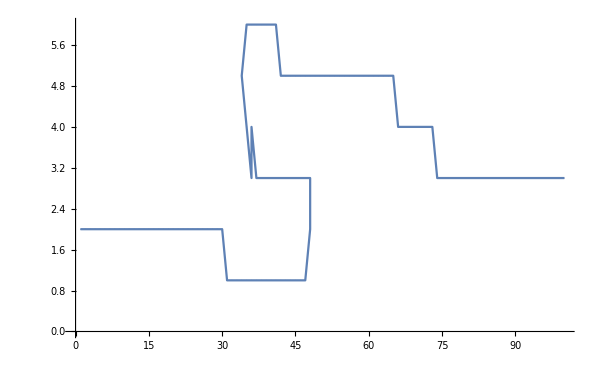

```mathematica
ListPlot[Reverse[points,2],PlotMarkers->{Automatic,1},Joined->True]
```

```mathematica
(*Search with bisection method until given precision*)
accuratePoints={};
p2s={};
p1s={};
For[i=2,i< Length[points],i++,
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.7//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.7//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res=result[[pt[[1]],pt[[2]]]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 30&&res1==res&&res2==res,k++,
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*2//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]+1);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]+1)/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*2//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]+1);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]+1)/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain"];
Print[pt];
];
p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res==res2,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/(Nμ-1)*(ptmid[[1]]-1);
If[μmid<1,μmid=1;ptmid[[1]]=(μmid-μmin)/(μmax-μmin)*(Nμ-1)+1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]]-1)/(Nγp-1));
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
accuratePoints=Append[accuratePoints,(pt1+pt2)/2];
];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0109167,0.0015601,1.}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.00732781,0.00135348,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.00753131,0.00136553,1.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.010933,0.00151232,1.} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.×10^-8,1.×10^-8,-0.0999463} is at the edge of the search region {1.×10^-8,100.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

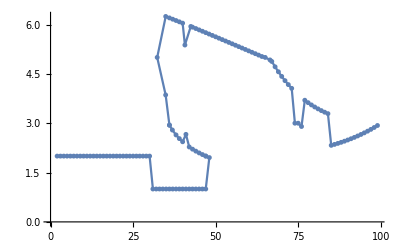

```mathematica
ListPlot[Reverse[accuratePoints,2],PlotMarkers->{Automatic,5},Joined->True]
```

```mathematica
toReassamble=accuratePoints;
k=0;
For[i=1,i< Length[toReassamble]&&k<300,i++,
k=k+1;
pt=toReassamble[[i]];
pt1=toReassamble[[i-1]];
pt2=toReassamble[[i+1]];
If[(pt-pt1).(pt2-pt)/Norm[(pt-pt1)]/Norm[pt2-pt]<-0.3,
placed=False;
j=i-1;
While[Not[placed],
ptp=toReassamble[[j]];
ptp2=toReassamble[[j+1]];
If[(ptp2-ptp).(pt2-ptp)/Norm[(ptp2-ptp)]/Norm[pt2-ptp]>-0.3,
Print["point placed ", j+1];
placed=True;
toReassamble=Delete[toReassamble,i+1];
toReassamble=Insert[toReassamble,pt2,j+1];
];
j=j-1;
];
i=i-1;
];
];
accuratePoints=toReassamble;
```

point placed 47

point placed 47

point placed 47

«10 more identical outputs»

point placed 48

point placed 48

point placed 48

point placed 49

point placed 52

point placed 54

point placed 58

point placed 59

point placed 60

point placed 61

point placed 65

point placed 66

point placed 68

point placed 71

point placed 74

point placed 74

point placed 74

«197 more identical outputs»

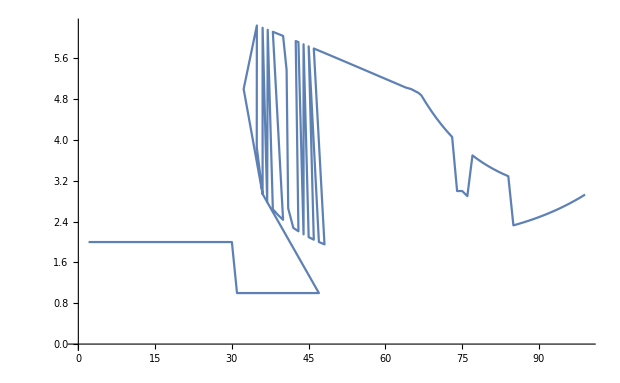

```mathematica
ListPlot[Reverse[toReassamble,2],Joined->True]
```

```mathematica
(*Interpolating fine boundary*)
PointNum=500;
sums=Prepend[Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]],{i,2,j}],{j,2,Length[accuratePoints]}],0];
interp=Interpolation[Transpose[{sums,accuratePoints}],Method->"Spline"];
initfinepts=Table[interp[Last[sums]/(PointNum)*i],{i,0,PointNum}];
```

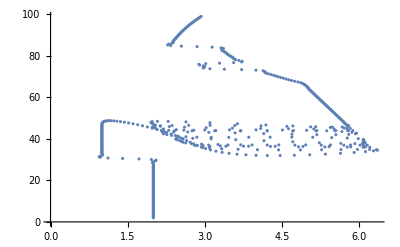

```mathematica
ListPlot[initfinepts]
```

```mathematica
(*Additional fine boundary search*)
finepts={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts],i++,
pt=initfinepts[[i]];
Δxy=initfinepts[[i+1]]-initfinepts[[i-1]];
pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.5//N;
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.5//N;
μ=μmin+(μmax-μmin)/(Nμ-1)*(pt[[1]]-1);
γp=γpmin*(γpmax/γpmin)^((pt[[2]])/Nγp);
If[μ<1,μ=1;pt[[1]]=(μ-μmin)/(μmax-μmin)*(Nμ-1)+1];

μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));

μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));

res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],For[k=1,k≤15&&res1==res&&res2==res,k++,pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];];
If[res==res1,pt1=pt,pt2=pt;];];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=2,k≤ 10&&res1==res,k++,
pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.2*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=2,k≤ 10&&res2==res,k++,
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.2*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/(Nμ-1)*(ptmid[[1]]-1);
If[μmid<1,μmid=1;ptmid[[1]]=(μmid-μmin)/(μmax-μmin)*(Nμ-1)+1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]]-1)/(Nγp-1));
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts=Append[finepts,(pt1+pt2)/2];
];
];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.00773594,0.00137449,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0100152,0.00150768,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.00819519,0.00140353,1.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {1.×10^-8,1.×10^-8,-0.0999463} is at the edge of the search region {1.×10^-8,100.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

All points for binary search are still in one domain. Ignoring point:

2

{2.,2.36019}

{{2.,2.36019},{1.,2.36019}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

All points for binary search are still in one domain. Ignoring point:

3

{2.,2.72038}

{{2.,2.72038},{1.,2.72038}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

All points for binary search are still in one domain. Ignoring point:

4

{2.,3.08057}

{{2.,3.08057},{1.,3.08057}}

All points for binary search are still in one domain. Ignoring point:

5

{2.,3.44076}

{{2.,3.44076},{1.,3.44076}}

All points for binary search are still in one domain. Ignoring point:

6

{2.,3.80095}

{{2.,3.80095},{1.,3.80095}}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

All points for binary search are still in one domain. Ignoring point:

7

{2.,4.16114}

{{2.,4.16114},{1.,4.16114}}

All points for binary search are still in one domain. Ignoring point:

8

{2.,4.52134}

{{2.,4.52134},{1.,4.52134}}

All points for binary search are still in one domain. Ignoring point:

9

{2.,4.88153}

{{2.,4.88153},{1.,4.88153}}

All points for binary search are still in one domain. Ignoring point:

10

{2.,5.24172}

{{2.,5.24172},{1.,5.24172}}

All points for binary search are still in one domain. Ignoring point:

11

{2.,5.60191}

{{2.,5.60191},{1.,5.60191}}

All points for binary search are still in one domain. Ignoring point:

12

{2.,5.9621}

{{2.,5.9621},{1.,5.9621}}

All points for binary search are still in one domain. Ignoring point:

13

{2.,6.32229}

{{2.,6.32229},{1.,6.32229}}

All points for binary search are still in one domain. Ignoring point:

14

{2.,6.68248}

{{2.,6.68248},{1.,6.68248}}

All points for binary search are still in one domain. Ignoring point:

15

{2.,7.04267}

{{2.,7.04267},{1.,7.04267}}

All points for binary search are still in one domain. Ignoring point:

16

{2.,7.40286}

{{2.,7.40286},{1.,7.40286}}

All points for binary search are still in one domain. Ignoring point:

17

{2.,7.76305}

{{2.,7.76305},{1.,7.76305}}

All points for binary search are still in one domain. Ignoring point:

18

{2.,8.12324}

{{2.,8.12324},{1.,8.12324}}

All points for binary search are still in one domain. Ignoring point:

19

{2.,8.48343}

{{2.,8.48343},{1.,8.48343}}

All points for binary search are still in one domain. Ignoring point:

20

{2.,8.84362}

{{2.,8.84362},{1.,8.84362}}

All points for binary search are still in one domain. Ignoring point:

21

{2.,9.20381}

{{2.,9.20381},{1.,9.20381}}

All points for binary search are still in one domain. Ignoring point:

22

{2.,9.56401}

{{2.,9.56401},{1.,9.56401}}

All points for binary search are still in one domain. Ignoring point:

23

{2.,9.9242}

{{2.,9.9242},{1.,9.9242}}

All points for binary search are still in one domain. Ignoring point:

24

{2.,10.2844}

{{2.,10.2844},{1.,10.2844}}

All points for binary search are still in one domain. Ignoring point:

25

{2.,10.6446}

{{2.,10.6446},{1.,10.6446}}

All points for binary search are still in one domain. Ignoring point:

26

{2.,11.0048}

{{2.,11.0048},{1.,11.0048}}

All points for binary search are still in one domain. Ignoring point:

27

{2.,11.365}

{{2.,11.365},{1.,11.365}}

All points for binary search are still in one domain. Ignoring point:

28

{2.,11.7251}

{{2.,11.7251},{1.,11.7251}}

All points for binary search are still in one domain. Ignoring point:

29

{2.,12.0853}

{{2.,12.0853},{1.,12.0853}}

All points for binary search are still in one domain. Ignoring point:

30

{2.,12.4455}

{{2.,12.4455},{1.,12.4455}}

All points for binary search are still in one domain. Ignoring point:

31

{2.,12.8057}

{{2.,12.8057},{1.,12.8057}}

All points for binary search are still in one domain. Ignoring point:

32

{2.,13.1659}

{{2.,13.1659},{1.,13.1659}}

All points for binary search are still in one domain. Ignoring point:

33

{2.,13.5261}

{{2.,13.5261},{1.,13.5261}}

All points for binary search are still in one domain. Ignoring point:

34

{2.,13.8863}

{{2.,13.8863},{1.,13.8863}}

All points for binary search are still in one domain. Ignoring point:

35

{2.,14.2465}

{{2.,14.2465},{1.,14.2465}}

All points for binary search are still in one domain. Ignoring point:

36

{2.,14.6067}

{{2.,14.6067},{1.,14.6067}}

All points for binary search are still in one domain. Ignoring point:

37

{2.,14.9669}

{{2.,14.9669},{1.,14.9669}}

All points for binary search are still in one domain. Ignoring point:

38

{2.,15.3271}

{{2.,15.3271},{1.,15.3271}}

All points for binary search are still in one domain. Ignoring point:

39

{2.,15.6872}

{{2.,15.6872},{1.,15.6872}}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

All points for binary search are still in one domain. Ignoring point:

40

{2.,16.0474}

{{2.,16.0474},{1.,16.0474}}

All points for binary search are still in one domain. Ignoring point:

41

{2.,16.4076}

{{2.,16.4076},{1.,16.4076}}

All points for binary search are still in one domain. Ignoring point:

42

{2.,16.7678}

{{2.,16.7678},{1.,16.7678}}

All points for binary search are still in one domain. Ignoring point:

43

{2.,17.128}

{{2.,17.128},{1.,17.128}}

All points for binary search are still in one domain. Ignoring point:

44

{2.,17.4882}

{{2.,17.4882},{1.,17.4882}}

All points for binary search are still in one domain. Ignoring point:

45

{2.,17.8484}

{{2.,17.8484},{1.,17.8484}}

All points for binary search are still in one domain. Ignoring point:

46

{2.,18.2086}

{{2.,18.2086},{1.,18.2086}}

All points for binary search are still in one domain. Ignoring point:

47

{2.,18.5688}

{{2.,18.5688},{1.,18.5688}}

All points for binary search are still in one domain. Ignoring point:

48

{2.,18.929}

{{2.,18.929},{1.,18.929}}

All points for binary search are still in one domain. Ignoring point:

49

{2.,19.2892}

{{2.,19.2892},{1.,19.2892}}

All points for binary search are still in one domain. Ignoring point:

50

{2.,19.6493}

{{2.,19.6493},{1.,19.6493}}

All points for binary search are still in one domain. Ignoring point:

51

{2.,20.0095}

{{2.,20.0095},{1.,20.0095}}

All points for binary search are still in one domain. Ignoring point:

52

{2.,20.3697}

{{2.,20.3697},{1.,20.3697}}

All points for binary search are still in one domain. Ignoring point:

53

{2.,20.7299}

{{2.,20.7299},{1.,20.7299}}

All points for binary search are still in one domain. Ignoring point:

54

{2.,21.0901}

{{2.,21.0901},{1.,21.0901}}

All points for binary search are still in one domain. Ignoring point:

55

{2.,21.4503}

{{2.,21.4503},{1.,21.4503}}

All points for binary search are still in one domain. Ignoring point:

56

{2.,21.8105}

{{2.,21.8105},{1.,21.8105}}

All points for binary search are still in one domain. Ignoring point:

57

{2.,22.1707}

{{2.,22.1707},{1.,22.1707}}

All points for binary search are still in one domain. Ignoring point:

58

{1.99999,22.5309}

{{1.99999,22.5309},{1.,22.5309}}

All points for binary search are still in one domain. Ignoring point:

59

{1.99999,22.8911}

{{1.99999,22.8911},{1.,22.8911}}

FindRoot::streg: The starting point {3.57356×10^-8,3.97062×10^-9,-0.1} is not in the search region {{1.×10^-8,1.×10^-8,-1.},{100.,100.,1.}}.

General::stop: Further output of FindRoot::streg will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{Eq1$2268881,Eq2$2268881,Eq3$2268881}==0,{{Qp,Qp0v2$2268881,N[1/10^8],100.},{Qm,Qm0v2$2268881,N[1/10^8],100.},{a,a0v2$2268881,-1.,1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 6 of {0} does not exist.

Part::partw: Part 5 of {0} does not exist.

Part::partw: Part 4 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

All points for binary search are still in one domain. Ignoring point:

63

{1.99994,24.3318}

{{1.99994,24.3318},{1.,24.3316}}

All points for binary search are still in one domain. Ignoring point:

64

{1.99992,24.692}

{{1.99992,24.692},{1.,24.6921}}

All points for binary search are still in one domain. Ignoring point:

65

{2.00002,25.0522}

{{2.00002,25.0522},{1.,25.0529}}

All points for binary search are still in one domain. Ignoring point:

66

{2.00024,25.4125}

{{2.00024,25.4125},{1.,25.413}}

All points for binary search are still in one domain. Ignoring point:

67

{2.00025,25.7727}

{{2.00025,25.7727},{1.,25.7716}}

All points for binary search are still in one domain. Ignoring point:

68

{1.99972,26.1327}

{{1.99972,26.1327},{1.,26.13}}

All points for binary search are still in one domain. Ignoring point:

69

{1.99897,26.4925}

{{1.99897,26.4925},{1.,26.4916}}

All points for binary search are still in one domain. Ignoring point:

70

{1.99927,26.8529}

{{1.99927,26.8529},{1.,26.8586}}

All points for binary search are still in one domain. Ignoring point:

71

{2.00173,27.2141}

{{2.00173,27.2141},{1.,27.2241}}

All points for binary search are still in one domain. Ignoring point:

72

{2.00409,27.5752}

{{2.00409,27.5752},{1.,27.5746}}

All points for binary search are still in one domain. Ignoring point:

73

{2.00143,27.9343}

{{2.00143,27.9343},{1.,27.9067}}

All points for binary search are still in one domain. Ignoring point:

74

{1.99091,28.2902}

{{1.99091,28.2902},{1.,28.2549}}

All points for binary search are still in one domain. Ignoring point:

75

{1.98468,28.6478}

{{1.98468,28.6478},{1.,28.6693}}

All points for binary search are still in one domain. Ignoring point:

76

{2.00133,29.0149}

{{2.00133,29.0149},{1.,29.132}}

All points for binary search are still in one domain. Ignoring point:

77

{2.04297,29.3923}

{{2.04297,29.3923},{1.,29.4968}}

All points for binary search are still in one domain. Ignoring point:

78

{2.05315,29.7567}

{{2.05315,29.7567},{1.,29.582}}

All points for binary search are still in one domain. Ignoring point:

79

{1.9624,30.0793}

{{1.9624,30.0793},{1.,29.3386}}

All points for binary search are still in one domain. Ignoring point:

80

{1.72199,30.3399}

{{1.72199,30.3399},{1.,29.2096}}

All points for binary search are still in one domain. Ignoring point:

81

{1.40247,30.5678}

{{1.40247,30.5678},{1.,29.3829}}

All points for binary search are still in one domain. Ignoring point:

82

{1.11693,30.8097}

{{1.11693,30.8097},{1.,29.8682}}

All points for binary search are still in one domain. Ignoring point:

83

{1.,31.1078}

{{1.,31.1078},{1.,30.7245}}

All points for binary search are still in one domain. Ignoring point:

84

{1.,31.459}

{{1.,31.459},{1.,31.4911}}

All points for binary search are still in one domain. Ignoring point:

85

{1.,31.8346}

{{1.,31.8346},{1.,31.9688}}

All points for binary search are still in one domain. Ignoring point:

86

{1.01246,32.2072}

{{1.01246,32.2072},{1.,32.2694}}

All points for binary search are still in one domain. Ignoring point:

87

{1.01313,32.5676}

{{1.01313,32.5676},{1.,32.546}}

All points for binary search are still in one domain. Ignoring point:

88

{1.00211,32.9233}

{{1.00211,32.9233},{1.,32.8874}}

All points for binary search are still in one domain. Ignoring point:

89

{1.,33.281}

{{1.,33.281},{1.,33.2704}}

All points for binary search are still in one domain. Ignoring point:

90

{1.,33.6415}

{{1.,33.6415},{1.,33.6497}}

All points for binary search are still in one domain. Ignoring point:

92

{1.00111,34.3636}

{{1.00111,34.3636},{1.,34.3648}}

All points for binary search are still in one domain. Ignoring point:

93

{1.00061,34.7236}

{{1.00061,34.7236},{1.,34.721}}

All points for binary search are still in one domain. Ignoring point:

94

{1.,35.0835}

{{1.,35.0835},{1.,35.0816}}

All points for binary search are still in one domain. Ignoring point:

95

{1.,35.4436}

{{1.,35.4436},{1.,35.4436}}

All points for binary search are still in one domain. Ignoring point:

96

{1.,35.8039}

{{1.,35.8039},{1.,35.8046}}

All points for binary search are still in one domain. Ignoring point:

97

{1.00006,36.1641}

{{1.00006,36.1641},{1.,36.1645}}

All points for binary search are still in one domain. Ignoring point:

98

{1.00007,36.5243}

{{1.00007,36.5243},{1.,36.5242}}

All points for binary search are still in one domain. Ignoring point:

100

{1.,37.2447}

{{1.,37.2447},{1.,37.2446}}

All points for binary search are still in one domain. Ignoring point:

101

{1.,37.6049}

{{1.,37.6049},{1.,37.6049}}

All points for binary search are still in one domain. Ignoring point:

102

{1.,37.9651}

{{1.,37.9651},{1.,37.9651}}

All points for binary search are still in one domain. Ignoring point:

105

{1.,39.0456}

{{1.,39.0456},{1.,39.0456}}

All points for binary search are still in one domain. Ignoring point:

179

{5.97249,34.8974}

{{5.97249,34.8974},{6.10276,33.4031}}

All points for binary search are still in one domain. Ignoring point:

180

{5.65305,34.8414}

{{5.65305,34.8414},{5.93907,33.3689}}

All points for binary search are still in one domain. Ignoring point:

182

{4.86244,34.6996}

{{4.86244,34.6996},{4.98325,33.2045}}

All points for binary search are still in one domain. Ignoring point:

183

{4.43829,34.6944}

{{4.43829,34.6944},{4.28458,33.2023}}

All points for binary search are still in one domain. Ignoring point:

191

{3.41199,36.4551}

{{3.41199,36.4551},{3.13889,37.93}}

All points for binary search are still in one domain. Ignoring point:

193

{4.37149,36.4397}

{{4.37149,36.4397},{4.55071,37.929}}

All points for binary search are still in one domain. Ignoring point:

194

{4.91204,36.3533}

{{4.91204,36.3533},{5.18843,37.8277}}

All points for binary search are still in one domain. Ignoring point:

195

{5.42076,36.243}

{{5.42076,36.243},{5.77052,37.7016}}

All points for binary search are still in one domain. Ignoring point:

200

{5.77485,36.0238}

{{5.77485,36.0238},{5.52589,34.5446}}

All points for binary search are still in one domain. Ignoring point:

202

{4.82425,36.2139}

{{4.82425,36.2139},{4.49628,34.7502}}

All points for binary search are still in one domain. Ignoring point:

203

{4.2805,36.342}

{{4.2805,36.342},{3.91756,34.8866}}

All points for binary search are still in one domain. Ignoring point:

204

{3.75703,36.4801}

{{3.75703,36.4801},{3.34775,35.037}}

All points for binary search are still in one domain. Ignoring point:

209

{3.07752,37.018}

{{3.07752,37.018},{2.81838,38.4955}}

All points for binary search are still in one domain. Ignoring point:

210

{3.45208,37.0602}

{{3.45208,37.0602},{3.33661,38.5557}}

All points for binary search are still in one domain. Ignoring point:

211

{3.92272,37.0833}

{{3.92272,37.0833},{3.87705,38.5826}}

All points for binary search are still in one domain. Ignoring point:

212

{4.44294,37.0904}

{{4.44294,37.0904},{4.44129,38.5904}}

All points for binary search are still in one domain. Ignoring point:

213

{4.96628,37.0844}

{{4.96628,37.0844},{4.9989,38.5841}}

All points for binary search are still in one domain. Ignoring point:

215

{5.83642,37.0457}

{{5.83642,37.0457},{5.95162,38.5413}}

All points for binary search are still in one domain. Ignoring point:

218

{6.02182,36.9666}

{{6.02182,36.9666},{6.15146,35.4723}}

All points for binary search are still in one domain. Ignoring point:

219

{5.70785,36.9519}

{{5.70785,36.9519},{5.73156,35.4521}}

All points for binary search are still in one domain. Ignoring point:

220

{5.26909,36.9547}

{{5.26909,36.9547},{5.22083,35.4555}}

All points for binary search are still in one domain. Ignoring point:

221

{4.75522,36.9826}

{{4.75522,36.9826},{4.62981,35.4879}}

All points for binary search are still in one domain. Ignoring point:

222

{4.21592,37.0431}

{{4.21592,37.0431},{3.98925,35.5603}}

All points for binary search are still in one domain. Ignoring point:

223

{3.70088,37.1438}

{{3.70088,37.1438},{3.32269,35.6922}}

All points for binary search are still in one domain. Ignoring point:

237

{3.60492,39.6171}

{{3.60492,39.6171},{4.59364,40.7451}}

All points for binary search are still in one domain. Ignoring point:

238

{4.15358,39.1181}

{{4.15358,39.1181},{5.16659,40.2244}}

All points for binary search are still in one domain. Ignoring point:

239

{4.7145,38.6011}

{{4.7145,38.6011},{5.72018,39.714}}

All points for binary search are still in one domain. Ignoring point:

253

{5.10316,40.7959}

{{5.10316,40.7959},{4.67635,39.3579}}

All points for binary search are still in one domain. Ignoring point:

254

{4.69564,40.8673}

{{4.69564,40.8673},{4.59919,39.3704}}

All points for binary search are still in one domain. Ignoring point:

255

{4.27364,40.8494}

{{4.27364,40.8494},{4.42036,39.3566}}

All points for binary search are still in one domain. Ignoring point:

256

{3.85795,40.785}

{{3.85795,40.785},{4.08569,39.3024}}

All points for binary search are still in one domain. Ignoring point:

257

{3.46866,40.7257}

{{3.46866,40.7257},{3.59485,39.231}}

All points for binary search are still in one domain. Ignoring point:

258

{3.12587,40.7232}

{{3.12587,40.7232},{2.88899,39.242}}

All points for binary search are still in one domain. Ignoring point:

268

{2.66996,43.298}

{{2.66996,43.298},{2.9453,44.7725}}

All points for binary search are still in one domain. Ignoring point:

269

{3.07967,43.1454}

{{3.07967,43.1454},{3.71931,44.5022}}

All points for binary search are still in one domain. Ignoring point:

270

{3.59134,42.8636}

{{3.59134,42.8636},{4.33695,44.1651}}

All points for binary search are still in one domain. Ignoring point:

271

{4.14938,42.5326}

{{4.14938,42.5326},{4.89216,43.8358}}

All points for binary search are still in one domain. Ignoring point:

272

{4.69815,42.2327}

{{4.69815,42.2327},{5.33954,43.5887}}

All points for binary search are still in one domain. Ignoring point:

281

{4.98372,44.143}

{{4.98372,44.143},{4.35302,42.782}}

All points for binary search are still in one domain. Ignoring point:

282

{4.51272,44.2914}

{{4.51272,44.2914},{4.19959,42.8245}}

All points for binary search are still in one domain. Ignoring point:

283

{3.99953,44.3531}

{{3.99953,44.3531},{3.91876,42.8553}}

All points for binary search are still in one domain. Ignoring point:

284

{3.4829,44.347}

{{3.4829,44.347},{3.57429,42.8498}}

All points for binary search are still in one domain. Ignoring point:

285

{3.00163,44.2922}

{{3.00163,44.2922},{3.23389,42.8103}}

All points for binary search are still in one domain. Ignoring point:

286

{2.59448,44.2077}

{{2.59448,44.2077},{2.96632,42.7545}}

All points for binary search are still in one domain. Ignoring point:

290

{2.41058,43.9314}

{{2.41058,43.9314},{2.53237,45.4264}}

All points for binary search are still in one domain. Ignoring point:

291

{2.75475,43.9198}

{{2.75475,43.9198},{2.76677,45.4198}}

All points for binary search are still in one domain. Ignoring point:

292

{3.19509,43.9251}

{{3.19509,43.9251},{3.15979,45.4247}}

All points for binary search are still in one domain. Ignoring point:

293

{3.69486,43.942}

{{3.69486,43.942},{3.63621,45.4408}}

All points for binary search are still in one domain. Ignoring point:

294

{4.21729,43.9651}

{{4.21729,43.9651},{4.1485,45.4635}}

All points for binary search are still in one domain. Ignoring point:

295

{4.72563,43.9893}

{{4.72563,43.9893},{4.65722,45.4877}}

All points for binary search are still in one domain. Ignoring point:

297

{5.55303,44.0196}

{{5.55303,44.0196},{5.53843,45.5195}}

All points for binary search are still in one domain. Ignoring point:

301

{5.53534,43.8912}

{{5.53534,43.8912},{5.78075,42.4114}}

All points for binary search are still in one domain. Ignoring point:

302

{5.16594,43.8425}

{{5.16594,43.8425},{5.30703,42.3492}}

All points for binary search are still in one domain. Ignoring point:

303

{4.71363,43.8136}

{{4.71363,43.8136},{4.75111,42.3141}}

All points for binary search are still in one domain. Ignoring point:

304

{4.21402,43.8187}

{{4.21402,43.8187},{4.12713,42.3212}}

All points for binary search are still in one domain. Ignoring point:

305

{3.70272,43.8722}

{{3.70272,43.8722},{3.45142,42.3934}}

All points for binary search are still in one domain. Ignoring point:

306

{3.21532,43.9884}

{{3.21532,43.9884},{2.73502,42.5674}}

All points for binary search are still in one domain. Ignoring point:

315

{2.68871,46.5515}

{{2.68871,46.5515},{2.41034,48.0254}}

All points for binary search are still in one domain. Ignoring point:

316

{3.10498,46.561}

{{3.10498,46.561},{3.24965,48.054}}

All points for binary search are still in one domain. Ignoring point:

317

{3.58613,46.4645}

{{3.58613,46.4645},{3.98603,47.9102}}

All points for binary search are still in one domain. Ignoring point:

318

{4.0964,46.2868}

{{4.0964,46.2868},{4.66129,47.6763}}

All points for binary search are still in one domain. Ignoring point:

319

{4.60006,46.0523}

{{4.60006,46.0523},{5.29103,47.3837}}

All points for binary search are still in one domain. Ignoring point:

325

{5.51768,44.8235}

{{5.51768,44.8235},{5.67644,43.3319}}

All points for binary search are still in one domain. Ignoring point:

326

{5.12323,44.825}

{{5.12323,44.825},{5.00939,43.3293}}

All points for binary search are still in one domain. Ignoring point:

327

{4.63131,44.8909}

{{4.63131,44.8909},{4.36173,43.4154}}

All points for binary search are still in one domain. Ignoring point:

329

{3.53876,45.1873}

{{3.53876,45.1873},{3.02094,43.7795}}

All points for binary search are still in one domain. Ignoring point:

330

{3.02999,45.4032}

{{3.02999,45.4032},{2.3572,44.0626}}

All points for binary search are still in one domain. Ignoring point:

343

{3.10194,47.7853}

{{3.10194,47.7853},{4.1229,48.8842}}

All points for binary search are still in one domain. Ignoring point:

344

{3.63703,47.2675}

{{3.63703,47.2675},{4.68466,48.3411}}

All points for binary search are still in one domain. Ignoring point:

345

{4.19173,46.7218}

{{4.19173,46.7218},{5.23341,47.8011}}

All points for binary search are still in one domain. Ignoring point:

346

{4.71637,46.2258}

{{4.71637,46.2258},{5.71467,47.3454}}

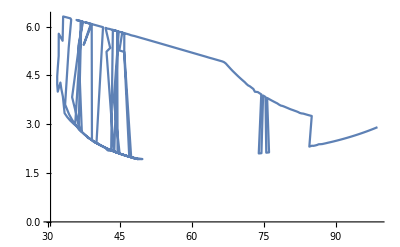

```mathematica
ListPlot[Reverse[finepts,2],Joined->True]
```

```mathematica
toReassamble=finepts;
k=0;
For[i=1,i< Length[toReassamble]&&k<300,i++,
k=k+1;
pt=toReassamble[[i]];
pt1=toReassamble[[i-1]];
pt2=toReassamble[[i+1]];
If[(pt-pt1).(pt2-pt)/Norm[(pt-pt1)]/Norm[pt2-pt]<-0.1,
placed=False;
j=i-1;
While[Not[placed],
ptp=toReassamble[[j]];
ptp2=toReassamble[[j+1]];
If[(ptp2-ptp).(pt2-ptp)/Norm[(ptp2-ptp)]/Norm[pt2-ptp]>-0.1,
Print["point placed ", j+1];
placed=True;
toReassamble=Delete[toReassamble,i+1];
toReassamble=Insert[toReassamble,pt2,j+1];
];
j=j-1;
];
i=i-1;
];
];
finepts=toReassamble;
```

point placed 20

point placed 17

point placed 23

point placed 23

point placed 23

point placed 20

point placed 18

point placed 16

point placed 14

point placed 13

point placed 11

point placed 9

point placed 8

point placed 6

point placed 6

point placed 5

point placed 4

point placed 3

point placed 3

point placed -40

point placed -40

point placed -40

«11 more identical outputs»

point placed -39

point placed -38

point placed -37

point placed -36

point placed -35

point placed -34

point placed -33

point placed -32

point placed -31

point placed -30

point placed -29

point placed -29

point placed -29

point placed -28

point placed -27

point placed -26

point placed -25

point placed -24

point placed -23

point placed -23

point placed -22

point placed -22

point placed -22

point placed -21

point placed -20

point placed -20

point placed -19

point placed -18

point placed -17

point placed -17

point placed -16

point placed -16

point placed -16

point placed -15

point placed -14

point placed -13

point placed -12

point placed -11

point placed -10

point placed 2

point placed 4

point placed 6

point placed 8

point placed 3

point placed -9

point placed 3

point placed 4

point placed 5

point placed 5

point placed 6

point placed 7

point placed 8

point placed 10

point placed 11

point placed 15

point placed 18

point placed 19

point placed 24

point placed 25

point placed 26

point placed 27

point placed 28

point placed 29

point placed 32

point placed 34

point placed 36

point placed 37

point placed 33

point placed 38

point placed 38

point placed 39

point placed 40

point placed 41

point placed 45

point placed 49

point placed 50

point placed 50

point placed 50

point placed 53

point placed 53

point placed 54

point placed 54

point placed 57

point placed 58

point placed 59

point placed 63

point placed 65

point placed 67

point placed 70

point placed 75

point placed 69

point placed 69

point placed 70

point placed 70

point placed 70

point placed 74

point placed 75

point placed 76

point placed 77

point placed 81

point placed 84

point placed 87

point placed 92

point placed 95

point placed 98

point placed 103

point placed 93

point placed 90

point placed 77

point placed 77

point placed 78

point placed 79

point placed 85

point placed 88

point placed 93

point placed 101

point placed 106

point placed 109

point placed 115

point placed 119

point placed 119

point placed 119

«27 more identical outputs»

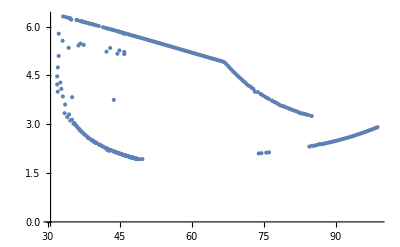

```mathematica
ListPlot[Reverse[finepts,2]]
```

```mathematica
(*Additional smoothing*)
PointNum2=700;
accuracy2=10^-7;
sums2=Prepend[Table[Sum[Norm[finepts[[i]]-finepts[[i-1]]],{i,2,j}],{j,2,Length[finepts]}],0];
interp2=Interpolation[Transpose[{sums2,finepts}],Method->"Spline"];
initfinepts2=Table[interp2[Last[sums2]/(PointNum2)*i],{i,0,PointNum2}];
finepts2={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts2],i++,
pt=initfinepts2[[i]];
Δxy=initfinepts2[[i+1]]-initfinepts2[[i-1]];
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1//N;
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1//N;
μ=μmin+(μmax-μmin)/(Nμ-1)*(pt[[1]]-1);
If[μ<1,μ=1;pt[[1]]=(μ-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp=γpmin*(γpmax/γpmin)^((pt[[2]]-1)/(Nγp-1));
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 10&&res1==res&&res2==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.03*k//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.03*k//N;
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=3,k≤ 10&&res1==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=3,k≤ 10&&res2==res,k++,
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy2,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/(Nμ-1)*(ptmid[[1]]-1);
If[μmid<1,μmid=1;ptmid[[1]]=(μmid-μmin)/(μmax-μmin)*(Nμ-1)+1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]]-1)/(Nγp-1));
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts2=Append[finepts2,(pt1+pt2)/2];
];
];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0221007,0.00146587,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0216922,0.00146159,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.0225092,0.00147008,1.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::reged: The point {0.0228359,0.00147339,1.} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

All points for binary search are still in one domain. Ignoring point:

5

{4.53426,39.9149}

{{4.53426,39.9149},{4.44691,39.6279}}

All points for binary search are still in one domain. Ignoring point:

9

{3.46262,41.9584}

{{3.46262,41.9584},{3.4785,42.258}}

All points for binary search are still in one domain. Ignoring point:

12

{3.67988,43.0033}

{{3.67988,43.0033},{3.5869,43.2885}}

All points for binary search are still in one domain. Ignoring point:

13

{5.27192,45.0577}

{{5.27192,45.0577},{5.0506,44.8552}}

All points for binary search are still in one domain. Ignoring point:

15

{5.76085,44.2654}

{{5.76085,44.2654},{5.71753,43.9686}}

All points for binary search are still in one domain. Ignoring point:

18

{3.28422,43.7342}

{{3.28422,43.7342},{3.3603,43.444}}

All points for binary search are still in one domain. Ignoring point:

19

{5.00104,44.8724}

{{5.00104,44.8724},{4.73045,44.7429}}

All points for binary search are still in one domain. Ignoring point:

21

{4.3196,45.3704}

{{4.3196,45.3704},{4.26138,45.6647}}

All points for binary search are still in one domain. Ignoring point:

22

{5.44524,47.0295}

{{5.44524,47.0295},{5.22894,46.8217}}

All points for binary search are still in one domain. Ignoring point:

23

{2.08675,47.6937}

{{2.08675,47.6937},{2.17291,47.4064}}

FindRoot::reged: The point {0.0107648,0.00120368,1.} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

All points for binary search are still in one domain. Ignoring point:

25

{4.7739,47.3051}

{{4.7739,47.3051},{4.4821,47.2355}}

All points for binary search are still in one domain. Ignoring point:

26

{1.96479,48.8313}

{{1.96479,48.8313},{1.99937,48.5333}}

All points for binary search are still in one domain. Ignoring point:

27

{2.75746,47.0711}

{{2.75746,47.0711},{2.8412,47.3592}}

All points for binary search are still in one domain. Ignoring point:

29

{2.87729,49.5182}

{{2.87729,49.5182},{2.83735,49.2208}}

All points for binary search are still in one domain. Ignoring point:

36

{3.30729,74.446}

{{3.30729,74.446},{3.02907,74.3338}}

FindRoot::reged: The point {1.×10^-8,1.×10^-8,-0.0999463} is at the edge of the search region {1.×10^-8,100.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

All points for binary search are still in one domain. Ignoring point:

40

{1.,70.6938}

{{1.,70.6938},{1.,70.5281}}

All points for binary search are still in one domain. Ignoring point:

41

{1.,22.3093}

{{1.,22.3093},{1.,22.156}}

All points for binary search are still in one domain. Ignoring point:

42

{1.,-22.8134}

{{1.,-22.8134},{1.,-22.9458}}

All points for binary search are still in one domain. Ignoring point:

43

{1.,-30.474}

{{1.,-30.474},{1.,-30.2396}}

All points for binary search are still in one domain. Ignoring point:

44

{1.,-7.20045}

{{1.,-7.20045},{1.,-7.00959}}

All points for binary search are still in one domain. Ignoring point:

45

{1.,23.1056}

{{1.,23.1056},{1.,23.2975}}

All points for binary search are still in one domain. Ignoring point:

46

{1.,39.9084}

{{1.,39.9084},{1.,40.1251}}

All points for binary search are still in one domain. Ignoring point:

47

{1.4018,42.7976}

{{1.4018,42.7976},{1.45531,43.0928}}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

All points for binary search are still in one domain. Ignoring point:

49

{3.41746,33.44}

{{3.41746,33.44},{3.41676,33.74}}

All points for binary search are still in one domain. Ignoring point:

50

{35.0934,38.7542}

{{35.0934,38.7542},{35.0205,39.0452}}

All points for binary search are still in one domain. Ignoring point:

51

{162.853,73.433}

{{162.853,73.433},{162.771,73.7217}}

All points for binary search are still in one domain. Ignoring point:

52

{322.524,119.735}

{{322.524,119.735},{322.437,120.022}}

All points for binary search are still in one domain. Ignoring point:

53

{441.01,157.519}

{{441.01,157.519},{440.91,157.801}}

All points for binary search are still in one domain. Ignoring point:

54

{478.573,175.461}

{{478.573,175.461},{478.297,175.578}}

All points for binary search are still in one domain. Ignoring point:

55

{449.04,176.406}

{{449.04,176.406},{449.071,176.108}}

All points for binary search are still in one domain. Ignoring point:

56

{371.073,164.475}

{{371.073,164.475},{371.125,164.18}}

All points for binary search are still in one domain. Ignoring point:

57

{263.333,143.79}

{{263.333,143.79},{263.392,143.496}}

All points for binary search are still in one domain. Ignoring point:

58

{144.48,118.47}

{{144.48,118.47},{144.545,118.177}}

All points for binary search are still in one domain. Ignoring point:

59

{33.1768,92.6379}

{{33.1768,92.6379},{33.248,92.3464}}

All points for binary search are still in one domain. Ignoring point:

60

{1.,70.1771}

{{1.,70.1771},{1.,69.8883}}

All points for binary search are still in one domain. Ignoring point:

61

{1.,52.349}

{{1.,52.349},{1.,52.0661}}

All points for binary search are still in one domain. Ignoring point:

62

{1.,38.7868}

{{1.,38.7868},{1.,38.5237}}

All points for binary search are still in one domain. Ignoring point:

63

{1.,29.099}

{{1.,29.099},{1.,29.022}}

All points for binary search are still in one domain. Ignoring point:

64

{1.,22.8943}

{{1.,22.8943},{1.,23.1765}}

All points for binary search are still in one domain. Ignoring point:

65

{1.,19.7815}

{{1.,19.7815},{1.,20.0807}}

All points for binary search are still in one domain. Ignoring point:

66

{1.,19.369}

{{1.,19.369},{1.,19.6689}}

All points for binary search are still in one domain. Ignoring point:

67

{1.,21.2657}

{{1.,21.2657},{1.,21.5646}}

All points for binary search are still in one domain. Ignoring point:

68

{1.,25.08}

{{1.,25.08},{1.,25.3769}}

All points for binary search are still in one domain. Ignoring point:

69

{1.,30.4207}

{{1.,30.4207},{1.,30.7135}}

All points for binary search are still in one domain. Ignoring point:

70

{20.6458,36.8982}

{{20.6458,36.8982},{20.5431,37.18}}

All points for binary search are still in one domain. Ignoring point:

71

{35.5299,44.1381}

{{35.5299,44.1381},{35.3669,44.3899}}

All points for binary search are still in one domain. Ignoring point:

72

{43.6191,51.7749}

{{43.6191,51.7749},{43.3717,51.9447}}

All points for binary search are still in one domain. Ignoring point:

73

{46.0336,59.4432}

{{46.0336,59.4432},{45.7337,59.4487}}

All points for binary search are still in one domain. Ignoring point:

74

{43.8938,66.7776}

{{43.8938,66.7776},{43.6312,66.6325}}

All points for binary search are still in one domain. Ignoring point:

75

{38.3201,73.4124}

{{38.3201,73.4124},{38.1186,73.1901}}

All points for binary search are still in one domain. Ignoring point:

76

{30.4327,78.9822}

{{30.4327,78.9822},{30.2837,78.7218}}

All points for binary search are still in one domain. Ignoring point:

77

{21.352,83.1216}

{{21.352,83.1216},{21.2515,82.8389}}

All points for binary search are still in one domain. Ignoring point:

78

{12.1984,85.4651}

{{12.1984,85.4651},{12.1549,85.1682}}

All points for binary search are still in one domain. Ignoring point:

79

{4.09208,85.6471}

{{4.09208,85.6471},{4.13606,85.3504}}

All points for binary search are still in one domain. Ignoring point:

80

{1.,83.3686}

{{1.,83.3686},{1.,83.1208}}

All points for binary search are still in one domain. Ignoring point:

81

{1.,78.901}

{{1.,78.901},{1.,78.7566}}

All points for binary search are still in one domain. Ignoring point:

82

{1.,72.8072}

{{1.,72.8072},{1.,72.7546}}

All points for binary search are still in one domain. Ignoring point:

83

{1.,65.6524}

{{1.,65.6524},{1.,65.6614}}

All points for binary search are still in one domain. Ignoring point:

84

{1.,58.0017}

{{1.,58.0017},{1.,58.0523}}

All points for binary search are still in one domain. Ignoring point:

85

{1.,50.4203}

{{1.,50.4203},{1.,50.5023}}

All points for binary search are still in one domain. Ignoring point:

86

{1.,43.4735}

{{1.,43.4735},{1.,43.5836}}

All points for binary search are still in one domain. Ignoring point:

87

{1.,37.7263}

{{1.,37.7263},{1.,37.8687}}

All points for binary search are still in one domain. Ignoring point:

88

{2.06946,33.744}

{{2.06946,33.744},{2.29693,33.9396}}

All points for binary search are still in one domain. Ignoring point:

89

{4.31118,32.0918}

{{4.31118,32.0918},{4.34931,32.3894}}

All points for binary search are still in one domain. Ignoring point:

90

{5.90067,33.2531}

{{5.90067,33.2531},{5.63341,33.3894}}

All points for binary search are still in one domain. Ignoring point:

91

{6.80863,36.9896}

{{6.80863,36.9896},{6.51119,37.0287}}

All points for binary search are still in one domain. Ignoring point:

92

{7.1421,42.6868}

{{7.1421,42.6868},{6.84214,42.6916}}

All points for binary search are still in one domain. Ignoring point:

93

{7.00932,49.7271}

{{7.00932,49.7271},{6.70958,49.7145}}

All points for binary search are still in one domain. Ignoring point:

94

{6.51849,57.4927}

{{6.51849,57.4927},{6.21942,57.4691}}

All points for binary search are still in one domain. Ignoring point:

95

{5.77786,65.3658}

{{5.77786,65.3658},{5.47954,65.334}}

All points for binary search are still in one domain. Ignoring point:

96

{4.89563,72.7288}

{{4.89563,72.7288},{4.59822,72.6895}}

All points for binary search are still in one domain. Ignoring point:

97

{3.98003,78.964}

{{3.98003,78.964},{3.68397,78.9155}}

All points for binary search are still in one domain. Ignoring point:

103

{2.45125,68.898}

{{2.45125,68.898},{2.75086,68.9131}}

All points for binary search are still in one domain. Ignoring point:

105

{3.38747,53.2415}

{{3.38747,53.2415},{3.6868,53.2614}}

All points for binary search are still in one domain. Ignoring point:

106

{3.90899,45.7831}

{{3.90899,45.7831},{4.2082,45.8049}}

All points for binary search are still in one domain. Ignoring point:

107

{4.39583,39.4092}

{{4.39583,39.4092},{4.69487,39.4333}}

All points for binary search are still in one domain. Ignoring point:

108

{4.79528,34.7482}

{{4.79528,34.7482},{5.09395,34.7764}}

All points for binary search are still in one domain. Ignoring point:

109

{5.05461,32.4284}

{{5.05461,32.4284},{5.34932,32.4845}}

All points for binary search are still in one domain. Ignoring point:

110

{5.12606,33.0111}

{{5.12606,33.0111},{4.82607,33.0081}}

All points for binary search are still in one domain. Ignoring point:

111

{5.01579,36.3249}

{{5.01579,36.3249},{4.71605,36.3124}}

All points for binary search are still in one domain. Ignoring point:

112

{4.76326,41.7466}

{{4.76326,41.7466},{4.46363,41.7318}}

All points for binary search are still in one domain. Ignoring point:

113

{4.4084,48.6464}

{{4.4084,48.6464},{4.10882,48.6306}}

All points for binary search are still in one domain. Ignoring point:

114

{3.99114,56.3944}

{{3.99114,56.3944},{3.69158,56.3781}}

All points for binary search are still in one domain. Ignoring point:

115

{3.5514,64.361}

{{3.5514,64.361},{3.25186,64.3444}}

All points for binary search are still in one domain. Ignoring point:

116

{3.12912,71.9162}

{{3.12912,71.9162},{2.82959,71.8995}}

All points for binary search are still in one domain. Ignoring point:

121

{2.62166,82.3703}

{{2.62166,82.3703},{2.92101,82.3901}}

All points for binary search are still in one domain. Ignoring point:

123

{3.3961,70.3205}

{{3.3961,70.3205},{3.6955,70.3395}}

All points for binary search are still in one domain. Ignoring point:

124

{3.88198,62.6327}

{{3.88198,62.6327},{4.18139,62.6515}}

All points for binary search are still in one domain. Ignoring point:

125

{4.38228,54.6725}

{{4.38228,54.6725},{4.6817,54.6913}}

All points for binary search are still in one domain. Ignoring point:

126

{4.85849,47.0673}

{{4.85849,47.0673},{5.1579,47.086}}

All points for binary search are still in one domain. Ignoring point:

128

{5.58453,35.43}

{{5.58453,35.43},{5.88395,35.4486}}

All points for binary search are still in one domain. Ignoring point:

129

{5.75734,32.6523}

{{5.75734,32.6523},{6.05676,32.671}}

All points for binary search are still in one domain. Ignoring point:

130

{5.75368,32.7108}

{{5.75368,32.7108},{5.45426,32.6921}}

All points for binary search are still in one domain. Ignoring point:

131

{5.57422,35.5965}

{{5.57422,35.5965},{5.2748,35.5779}}

All points for binary search are still in one domain. Ignoring point:

133

{4.8389,47.4089}

{{4.8389,47.4089},{4.53948,47.3902}}

All points for binary search are still in one domain. Ignoring point:

134

{4.36082,55.0775}

{{4.36082,55.0775},{4.0614,55.0588}}

All points for binary search are still in one domain. Ignoring point:

136

{3.37829,70.7948}

{{3.37829,70.7948},{3.07888,70.776}}

All points for binary search are still in one domain. Ignoring point:

137

{2.95164,77.5855}

{{2.95164,77.5855},{2.65224,77.5667}}

All points for binary search are still in one domain. Ignoring point:

138

{2.61992,82.8257}

{{2.61992,82.8257},{2.32053,82.8066}}

All points for binary search are still in one domain. Ignoring point:

142

{2.83603,78.6859}

{{2.83603,78.6859},{3.1355,78.7038}}

All points for binary search are still in one domain. Ignoring point:

143

{3.22731,72.1678}

{{3.22731,72.1678},{3.52677,72.1858}}

All points for binary search are still in one domain. Ignoring point:

144

{3.68105,64.6329}

{{3.68105,64.6329},{3.98051,64.6509}}

All points for binary search are still in one domain. Ignoring point:

145

{4.1585,56.7103}

{{4.1585,56.7103},{4.45795,56.7284}}

All points for binary search are still in one domain. Ignoring point:

146

{4.62088,49.0294}

{{4.62088,49.0294},{4.92034,49.0474}}

All points for binary search are still in one domain. Ignoring point:

147

{5.02944,42.2194}

{{5.02944,42.2194},{5.32891,42.2373}}

All points for binary search are still in one domain. Ignoring point:

153

{4.67393,47.0236}

{{4.67393,47.0236},{4.37451,47.005}}

All points for binary search are still in one domain. Ignoring point:

154

{4.20892,54.5581}

{{4.20892,54.5581},{3.90948,54.5397}}

All points for binary search are still in one domain. Ignoring point:

155

{3.72396,62.5198}

{{3.72396,62.5198},{3.4245,62.5017}}

All points for binary search are still in one domain. Ignoring point:

156

{3.25944,70.2771}

{{3.25944,70.2771},{2.95996,70.2594}}

All points for binary search are still in one domain. Ignoring point:

157

{2.85577,77.1985}

{{2.85577,77.1985},{2.55625,77.1814}}

All points for binary search are still in one domain. Ignoring point:

161

{2.62702,84.3552}

{{2.62702,84.3552},{2.92597,84.3803}}

All points for binary search are still in one domain. Ignoring point:

162

{2.99481,79.7162}

{{2.99481,79.7162},{3.29393,79.7392}}

All points for binary search are still in one domain. Ignoring point:

163

{3.47358,73.3503}

{{3.47358,73.3503},{3.77276,73.3725}}

All points for binary search are still in one domain. Ignoring point:

164

{4.02009,65.8867}

{{4.02009,65.8867},{4.31931,65.9084}}

All points for binary search are still in one domain. Ignoring point:

165

{4.5911,57.9547}

{{4.5911,57.9547},{4.89034,57.9761}}

All points for binary search are still in one domain. Ignoring point:

166

{5.14336,50.1835}

{{5.14336,50.1835},{5.44261,50.2046}}

All points for binary search are still in one domain. Ignoring point:

174

{4.79904,53.6285}

{{4.79904,53.6285},{4.49983,53.6067}}

All points for binary search are still in one domain. Ignoring point:

175

{4.22244,61.586}

{{4.22244,61.586},{3.92322,61.5643}}

All points for binary search are still in one domain. Ignoring point:

176

{3.65576,69.4321}

{{3.65576,69.4321},{3.35654,69.4106}}

All points for binary search are still in one domain. Ignoring point:

177

{3.14423,76.5367}

{{3.14423,76.5367},{2.845,76.5152}}

All points for binary search are still in one domain. Ignoring point:

178

{2.73307,82.2694}

{{2.73307,82.2694},{2.43383,82.248}}

All points for binary search are still in one domain. Ignoring point:

182

{2.84762,80.9428}

{{2.84762,80.9428},{3.14682,80.9647}}

All points for binary search are still in one domain. Ignoring point:

183

{3.29555,74.8156}

{{3.29555,74.8156},{3.59475,74.8374}}

All points for binary search are still in one domain. Ignoring point:

184

{3.82961,67.4953}

{{3.82961,67.4953},{4.12882,67.5172}}

All points for binary search are still in one domain. Ignoring point:

185

{4.40415,59.612}

{{4.40415,59.612},{4.70336,59.6338}}

All points for binary search are still in one domain. Ignoring point:

193

{5.41977,45.7968}

{{5.41977,45.7968},{5.12055,45.7751}}

All points for binary search are still in one domain. Ignoring point:

195

{4.317,61.0292}

{{4.317,61.0292},{4.01778,61.0075}}

All points for binary search are still in one domain. Ignoring point:

196

{3.7459,68.9152}

{{3.7459,68.9152},{3.44669,68.8935}}

All points for binary search are still in one domain. Ignoring point:

197

{3.22291,76.1368}

{{3.22291,76.1368},{2.92369,76.1151}}

All points for binary search are still in one domain. Ignoring point:

198

{2.79394,82.061}

{{2.79394,82.061},{2.49472,82.0393}}

All points for binary search are still in one domain. Ignoring point:

202

{2.80915,81.882}

{{2.80915,81.882},{3.10837,81.9037}}

All points for binary search are still in one domain. Ignoring point:

203

{3.242,75.9208}

{{3.242,75.9208},{3.54121,75.9425}}

All points for binary search are still in one domain. Ignoring point:

204

{3.76646,68.6962}

{{3.76646,68.6962},{4.06568,68.718}}

All points for binary search are still in one domain. Ignoring point:

205

{4.3367,60.841}

{{4.3367,60.841},{4.63591,60.8627}}

All points for binary search are still in one domain. Ignoring point:

207

{5.43104,45.7684}

{{5.43104,45.7684},{5.73026,45.7901}}

All points for binary search are still in one domain. Ignoring point:

213

{5.44721,45.6304}

{{5.44721,45.6304},{5.14799,45.6088}}

All points for binary search are still in one domain. Ignoring point:

215

{4.35568,60.7415}

{{4.35568,60.7415},{4.05646,60.7199}}

All points for binary search are still in one domain. Ignoring point:

216

{3.78516,68.6501}

{{3.78516,68.6501},{3.48593,68.6285}}

All points for binary search are still in one domain. Ignoring point:

217

{3.25959,75.9484}

{{3.25959,75.9484},{2.96036,75.9269}}

All points for binary search are still in one domain. Ignoring point:

218

{2.82507,82.0023}

{{2.82507,82.0023},{2.52583,81.9809}}

All points for binary search are still in one domain. Ignoring point:

222

{2.80461,82.6537}

{{2.80461,82.6537},{3.1038,82.6758}}

All points for binary search are still in one domain. Ignoring point:

223

{3.23441,76.8241}

{{3.23441,76.8241},{3.53361,76.8461}}

All points for binary search are still in one domain. Ignoring point:

224

{3.75813,69.6794}

{{3.75813,69.6794},{4.05733,69.7013}}

All points for binary search are still in one domain. Ignoring point:

225

{4.32906,61.8515}

{{4.32906,61.8515},{4.62827,61.8733}}

All points for binary search are still in one domain. Ignoring point:

226

{4.90052,53.9723}

{{4.90052,53.9723},{5.19974,53.9939}}

All points for binary search are still in one domain. Ignoring point:

227

{5.42581,46.6735}

{{5.42581,46.6735},{5.72505,46.6949}}

All points for binary search are still in one domain. Ignoring point:

233

{5.38525,45.3346}

{{5.38525,45.3346},{5.08614,45.3115}}

All points for binary search are still in one domain. Ignoring point:

234

{4.84158,52.4521}

{{4.84158,52.4521},{4.54243,52.4295}}

All points for binary search are still in one domain. Ignoring point:

235

{4.25455,60.2862}

{{4.25455,60.2862},{3.95537,60.264}}

All points for binary search are still in one domain. Ignoring point:

236

{3.67402,68.2069}

{{3.67402,68.2069},{3.3748,68.1853}}

All points for binary search are still in one domain. Ignoring point:

237

{3.14983,75.5845}

{{3.14983,75.5845},{2.85055,75.5637}}

All points for binary search are still in one domain. Ignoring point:

238

{2.7318,81.789}

{{2.7318,81.789},{2.43242,81.7698}}

All points for binary search are still in one domain. Ignoring point:

242

{2.99923,83.6125}

{{2.99923,83.6125},{3.29765,83.6432}}

All points for binary search are still in one domain. Ignoring point:

248

{6.33146,41.719}

{{6.33146,41.719},{6.63115,41.7326}}

All points for binary search are still in one domain. Ignoring point:

249

{6.46741,37.1207}

{{6.46741,37.1207},{6.76741,37.1201}}

All points for binary search are still in one domain. Ignoring point:

251

{5.83675,35.447}

{{5.83675,35.447},{5.55148,35.3542}}

All points for binary search are still in one domain. Ignoring point:

252

{5.07912,38.6647}

{{5.07912,38.6647},{4.78487,38.6062}}

All points for binary search are still in one domain. Ignoring point:

253

{4.15328,43.9201}

{{4.15328,43.9201},{3.85704,43.8727}}

All points for binary search are still in one domain. Ignoring point:

254

{3.16709,50.6228}

{{3.16709,50.6228},{2.86978,50.5826}}

All points for binary search are still in one domain. Ignoring point:

256

{1.445,66.0077}

{{1.445,66.0077},{1.14608,65.9823}}

All points for binary search are still in one domain. Ignoring point:

257

{1.,73.5089}

{{1.,73.5089},{1.,73.4946}}

All points for binary search are still in one domain. Ignoring point:

258

{1.,80.0952}

{{1.,80.0952},{1.,80.0998}}

All points for binary search are still in one domain. Ignoring point:

259

{1.10532,85.1761}

{{1.10532,85.1761},{1.,85.2219}}

All points for binary search are still in one domain. Ignoring point:

260

{2.02171,88.1611}

{{2.02171,88.1611},{1.78156,88.3409}}

All points for binary search are still in one domain. Ignoring point:

261

{3.60979,88.5214}

{{3.60979,88.5214},{3.7411,88.7911}}

All points for binary search are still in one domain. Ignoring point:

262

{5.71972,86.3609}

{{5.71972,86.3609},{5.96552,86.5328}}

All points for binary search are still in one domain. Ignoring point:

263

{8.0638,82.1554}

{{8.0638,82.1554},{8.33589,82.2818}}

All points for binary search are still in one domain. Ignoring point:

264

{10.3526,76.3854}

{{10.3526,76.3854},{10.637,76.4808}}

All points for binary search are still in one domain. Ignoring point:

265

{12.2966,69.5315}

{{12.2966,69.5315},{12.5891,69.598}}

All points for binary search are still in one domain. Ignoring point:

266

{13.6064,62.074}

{{13.6064,62.074},{13.9045,62.1076}}

All points for binary search are still in one domain. Ignoring point:

267

{13.9925,54.4935}

{{13.9925,54.4935},{14.2924,54.4853}}

All points for binary search are still in one domain. Ignoring point:

268

{13.1999,47.2827}

{{13.1999,47.2827},{13.4935,47.2209}}

All points for binary search are still in one domain. Ignoring point:

269

{11.155,40.9984}

{{11.155,40.9984},{11.425,40.8677}}

All points for binary search are still in one domain. Ignoring point:

270

{7.84395,36.2189}

{{7.84395,36.2189},{8.05033,36.0012}}

All points for binary search are still in one domain. Ignoring point:

271

{3.26154,33.5168}

{{3.26154,33.5168},{3.34788,33.2295}}

All points for binary search are still in one domain. Ignoring point:

272

{1.,33.205}

{{1.,33.205},{1.,32.9087}}

All points for binary search are still in one domain. Ignoring point:

273

{1.,35.2277}

{{1.,35.2277},{1.,34.9779}}

All points for binary search are still in one domain. Ignoring point:

274

{1.,39.5011}

{{1.,39.5011},{1.,39.3503}}

All points for binary search are still in one domain. Ignoring point:

275

{1.,45.894}

{{1.,45.894},{1.,45.853}}

All points for binary search are still in one domain. Ignoring point:

276

{1.,53.8368}

{{1.,53.8368},{1.,53.8688}}

All points for binary search are still in one domain. Ignoring point:

277

{1.,62.5215}

{{1.,62.5215},{1.,62.5982}}

All points for binary search are still in one domain. Ignoring point:

278

{1.,71.1378}

{{1.,71.1378},{1.,71.247}}

All points for binary search are still in one domain. Ignoring point:

279

{1.,78.8754}

{{1.,78.8754},{1.,79.0148}}

All points for binary search are still in one domain. Ignoring point:

280

{1.,84.924}

{{1.,84.924},{1.,85.1025}}

All points for binary search are still in one domain. Ignoring point:

281

{1.57334,88.4733}

{{1.57334,88.4733},{1.41081,88.7255}}

All points for binary search are still in one domain. Ignoring point:

282

{4.21776,88.8184}

{{4.21776,88.8184},{4.3562,89.0846}}

All points for binary search are still in one domain. Ignoring point:

283

{6.03126,86.1545}

{{6.03126,86.1545},{6.31189,86.2605}}

All points for binary search are still in one domain. Ignoring point:

284

{7.12182,81.133}

{{7.12182,81.133},{7.41918,81.1727}}

All points for binary search are still in one domain. Ignoring point:

285

{7.59889,74.4093}

{{7.59889,74.4093},{7.89874,74.4186}}

All points for binary search are still in one domain. Ignoring point:

286

{7.57188,66.6384}

{{7.57188,66.6384},{7.87177,66.63}}

All points for binary search are still in one domain. Ignoring point:

287

{7.15025,58.4755}

{{7.15025,58.4755},{7.44951,58.4545}}

All points for binary search are still in one domain. Ignoring point:

288

{6.44342,50.5757}

{{6.44342,50.5757},{6.74172,50.5438}}

All points for binary search are still in one domain. Ignoring point:

289

{5.56082,43.5942}

{{5.56082,43.5942},{5.85759,43.5503}}

All points for binary search are still in one domain. Ignoring point:

290

{4.61189,38.1862}

{{4.61189,38.1862},{4.90512,38.1228}}

All points for binary search are still in one domain. Ignoring point:

291

{3.70606,35.0067}

{{3.70606,35.0067},{3.97704,34.878}}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

All points for binary search are still in one domain. Ignoring point:

293

{2.39065,37.2699}

{{2.39065,37.2699},{2.09301,37.2323}}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

All points for binary search are still in one domain. Ignoring point:

297

{1.68106,64.3992}

{{1.68106,64.3992},{1.38107,64.401}}

All points for binary search are still in one domain. Ignoring point:

298

{1.77064,72.2545}

{{1.77064,72.2545},{1.47068,72.2593}}

All points for binary search are still in one domain. Ignoring point:

304

{2.81914,82.6284}

{{2.81914,82.6284},{3.11905,82.6358}}

All points for binary search are still in one domain. Ignoring point:

305

{2.93938,76.3831}

{{2.93938,76.3831},{3.23934,76.3879}}

All points for binary search are still in one domain. Ignoring point:

306

{3.0356,68.9894}

{{3.0356,68.9894},{3.33558,68.9927}}

All points for binary search are still in one domain. Ignoring point:

307

{3.1083,61.0643}

{{3.1083,61.0643},{3.40829,61.0667}}

All points for binary search are still in one domain. Ignoring point:

308

{3.15797,53.2249}

{{3.15797,53.2249},{3.45796,53.2265}}

All points for binary search are still in one domain. Ignoring point:

309

{3.18511,46.0882}

{{3.18511,46.0882},{3.48511,46.0889}}

All points for binary search are still in one domain. Ignoring point:

310

{3.19023,40.2711}

{{3.19023,40.2711},{3.49022,40.2708}}

All points for binary search are still in one domain. Ignoring point:

311

{3.17381,36.3908}

{{3.17381,36.3908},{3.47379,36.3877}}

All points for binary search are still in one domain. Ignoring point:

314

{3.00676,40.7908}

{{3.00676,40.7908},{2.7068,40.7862}}

All points for binary search are still in one domain. Ignoring point:

315

{2.92396,46.7893}

{{2.92396,46.7893},{2.62399,46.7855}}

All points for binary search are still in one domain. Ignoring point:

316

{2.83585,54.054}

{{2.83585,54.054},{2.53587,54.0505}}

All points for binary search are still in one domain. Ignoring point:

317

{2.74742,61.9665}

{{2.74742,61.9665},{2.44744,61.9633}}

All points for binary search are still in one domain. Ignoring point:

318

{2.6637,69.9089}

{{2.6637,69.9089},{2.36371,69.9058}}

All points for binary search are still in one domain. Ignoring point:

325

{2.58709,79.2544}

{{2.58709,79.2544},{2.88707,79.2575}}

All points for binary search are still in one domain. Ignoring point:

326

{2.65873,72.2242}

{{2.65873,72.2242},{2.95872,72.2273}}

All points for binary search are still in one domain. Ignoring point:

327

{2.73774,64.4337}

{{2.73774,64.4337},{3.03773,64.4367}}

All points for binary search are still in one domain. Ignoring point:

328

{2.81815,56.4998}

{{2.81815,56.4998},{3.11813,56.5029}}

All points for binary search are still in one domain. Ignoring point:

329

{2.89397,49.0398}

{{2.89397,49.0398},{3.19396,49.0428}}

All points for binary search are still in one domain. Ignoring point:

331

{3.00802,38.009}

{{3.00802,38.009},{3.308,38.0122}}

All points for binary search are still in one domain. Ignoring point:

334

{3.00458,39.4798}

{{3.00458,39.4798},{2.70459,39.4771}}

All points for binary search are still in one domain. Ignoring point:

335

{2.95548,44.855}

{{2.95548,44.855},{2.65549,44.8522}}

All points for binary search are still in one domain. Ignoring point:

338

{2.73895,67.4584}

{{2.73895,67.4584},{2.43896,67.4555}}

All points for binary search are still in one domain. Ignoring point:

339

{2.66255,75.0902}

{{2.66255,75.0902},{2.36256,75.0871}}

All points for binary search are still in one domain. Ignoring point:

340

{2.59346,81.7397}

{{2.59346,81.7397},{2.29348,81.7365}}

All points for binary search are still in one domain. Ignoring point:

346

{2.57621,75.2386}

{{2.57621,75.2386},{2.8762,75.2409}}

All points for binary search are still in one domain. Ignoring point:

347

{2.63472,67.6528}

{{2.63472,67.6528},{2.93471,67.6552}}

All points for binary search are still in one domain. Ignoring point:

349

{2.76757,51.9987}

{{2.76757,51.9987},{3.06755,52.0014}}

All points for binary search are still in one domain. Ignoring point:

350

{2.83291,45.1631}

{{2.83291,45.1631},{3.13289,45.1661}}

All points for binary search are still in one domain. Ignoring point:

351

{2.89152,39.8102}

{{2.89152,39.8102},{3.1915,39.8139}}

All points for binary search are still in one domain. Ignoring point:

354

{2.98417,38.3425}

{{2.98417,38.3425},{2.68417,38.343}}

All points for binary search are still in one domain. Ignoring point:

355

{2.98064,43.001}

{{2.98064,43.001},{2.68065,43.0004}}

All points for binary search are still in one domain. Ignoring point:

356

{2.9613,49.3727}

{{2.9613,49.3727},{2.6613,49.3715}}

All points for binary search are still in one domain. Ignoring point:

357

{2.92742,56.8432}

{{2.92742,56.8432},{2.62742,56.8416}}

All points for binary search are still in one domain. Ignoring point:

359

{2.82121,72.6243}

{{2.82121,72.6243},{2.52122,72.6217}}

All points for binary search are still in one domain. Ignoring point:

360

{2.75146,79.7066}

{{2.75146,79.7066},{2.45148,79.7031}}

All points for binary search are still in one domain. Ignoring point:

361

{2.67232,85.431}

{{2.67232,85.431},{2.37237,85.4257}}

All points for binary search are still in one domain. Ignoring point:

370

{2.25533,48.3973}

{{2.25533,48.3973},{2.55529,48.4022}}

All points for binary search are still in one domain. Ignoring point:

374

{3.28351,37.0902}

{{3.28351,37.0902},{2.98848,37.1447}}

All points for binary search are still in one domain. Ignoring point:

376

{4.12821,45.8641}

{{4.12821,45.8641},{3.82884,45.8836}}

All points for binary search are still in one domain. Ignoring point:

377

{4.49581,52.5859}

{{4.49581,52.5859},{4.19611,52.5992}}

All points for binary search are still in one domain. Ignoring point:

378

{4.76128,60.1171}

{{4.76128,60.1171},{4.46137,60.1245}}

All points for binary search are still in one domain. Ignoring point:

380

{4.78887,75.366}

{{4.78887,75.366},{4.48901,75.357}}

All points for binary search are still in one domain. Ignoring point:

381

{4.45254,81.9629}

{{4.45254,81.9629},{4.15355,81.9382}}

All points for binary search are still in one domain. Ignoring point:

382

{3.81713,87.1276}

{{3.81713,87.1276},{3.52264,87.0704}}

All points for binary search are still in one domain. Ignoring point:

383

{2.83343,90.2997}

{{2.83343,90.2997},{2.5769,90.1441}}

All points for binary search are still in one domain. Ignoring point:

384

{1.47291,90.9943}

{{1.47291,90.9943},{1.56681,90.7094}}

All points for binary search are still in one domain. Ignoring point:

385

{1.,89.3232}

{{1.,89.3232},{1.,89.1672}}

All points for binary search are still in one domain. Ignoring point:

386

{1.,85.6813}

{{1.,85.6813},{1.,85.5828}}

All points for binary search are still in one domain. Ignoring point:

387

{1.,80.4652}

{{1.,80.4652},{1.,80.402}}

All points for binary search are still in one domain. Ignoring point:

388

{1.,74.0712}

{{1.,74.0712},{1.,74.0384}}

All points for binary search are still in one domain. Ignoring point:

389

{1.,66.8961}

{{1.,66.8961},{1.,66.8949}}

All points for binary search are still in one domain. Ignoring point:

390

{1.,59.3364}

{{1.,59.3364},{1.,59.3706}}

All points for binary search are still in one domain. Ignoring point:

391

{1.,51.7983}

{{1.,51.7983},{1.,51.8683}}

All points for binary search are still in one domain. Ignoring point:

392

{1.,44.7453}

{{1.,44.7453},{1.,44.8474}}

All points for binary search are still in one domain. Ignoring point:

393

{1.78896,38.6611}

{{1.78896,38.6611},{2.05706,38.7957}}

All points for binary search are still in one domain. Ignoring point:

394

{4.55745,34.0294}

{{4.55745,34.0294},{4.79929,34.2069}}

All points for binary search are still in one domain. Ignoring point:

395

{7.16732,31.3339}

{{7.16732,31.3339},{7.32649,31.5882}}

All points for binary search are still in one domain. Ignoring point:

396

{9.30393,31.0586}

{{9.30393,31.0586},{9.13607,31.3072}}

All points for binary search are still in one domain. Ignoring point:

397

{10.6526,33.687}

{{10.6526,33.687},{10.3583,33.7447}}

All points for binary search are still in one domain. Ignoring point:

398

{10.9653,39.5245}

{{10.9653,39.5245},{10.6653,39.5185}}

All points for binary search are still in one domain. Ignoring point:

399

{10.3682,47.871}

{{10.3682,47.871},{10.0697,47.8406}}

All points for binary search are still in one domain. Ignoring point:

400

{9.11868,57.6743}

{{9.11868,57.6743},{8.82177,57.6313}}

All points for binary search are still in one domain. Ignoring point:

401

{7.47439,67.8819}

{{7.47439,67.8819},{7.1788,67.8306}}

All points for binary search are still in one domain. Ignoring point:

402

{5.69282,77.4414}

{{5.69282,77.4414},{5.39851,77.3832}}

All points for binary search are still in one domain. Ignoring point:

403

{4.0315,85.3003}

{{4.0315,85.3003},{3.73896,85.2338}}

All points for binary search are still in one domain. Ignoring point:

405

{2.05415,91.9158}

{{2.05415,91.9158},{2.1435,91.6294}}

All points for binary search are still in one domain. Ignoring point:

406

{1.9096,90.1445}

{{1.9096,90.1445},{2.20953,90.151}}

All points for binary search are still in one domain. Ignoring point:

409

{3.49972,72.2795}

{{3.49972,72.2795},{3.79821,72.3096}}

All points for binary search are still in one domain. Ignoring point:

410

{4.28022,64.5196}

{{4.28022,64.5196},{4.57882,64.5485}}

All points for binary search are still in one domain. Ignoring point:

411

{4.97388,57.0468}

{{4.97388,57.0468},{5.2728,57.0723}}

All points for binary search are still in one domain. Ignoring point:

416

{6.44919,29.1561}

{{6.44919,29.1561},{6.74907,29.1645}}

All points for binary search are still in one domain. Ignoring point:

417

{6.48866,26.605}

{{6.48866,26.605},{6.78788,26.5834}}

All points for binary search are still in one domain. Ignoring point:

418

{6.32921,27.4912}

{{6.32921,27.4912},{6.03048,27.4636}}

All points for binary search are still in one domain. Ignoring point:

419

{5.91898,32.7859}

{{5.91898,32.7859},{5.61975,32.7645}}

All points for binary search are still in one domain. Ignoring point:

420

{5.31657,41.6337}

{{5.31657,41.6337},{5.01722,41.614}}

All points for binary search are still in one domain. Ignoring point:

421

{4.61122,52.6722}

{{4.61122,52.6722},{4.31179,52.6536}}

All points for binary search are still in one domain. Ignoring point:

422

{3.89216,64.5393}

{{3.89216,64.5393},{3.59267,64.5217}}

All points for binary search are still in one domain. Ignoring point:

423

{3.24863,75.8728}

{{3.24863,75.8728},{2.94907,75.8566}}

All points for binary search are still in one domain. Ignoring point:

424

{2.76988,85.3104}

{{2.76988,85.3104},{2.47019,85.2969}}

All points for binary search are still in one domain. Ignoring point:

428

{3.50758,87.1011}

{{3.50758,87.1011},{3.80602,87.1317}}

All points for binary search are still in one domain. Ignoring point:

429

{4.15165,80.2818}

{{4.15165,80.2818},{4.45049,80.3082}}

All points for binary search are still in one domain. Ignoring point:

430

{4.83513,72.0731}

{{4.83513,72.0731},{5.13422,72.0965}}

All points for binary search are still in one domain. Ignoring point:

431

{5.48467,63.2482}

{{5.48467,63.2482},{5.78397,63.2686}}

All points for binary search are still in one domain. Ignoring point:

432

{6.02692,54.5804}

{{6.02692,54.5804},{6.32647,54.5969}}

All points for binary search are still in one domain. Ignoring point:

433

{6.38856,46.843}

{{6.38856,46.843},{6.68839,46.8532}}

All points for binary search are still in one domain. Ignoring point:

434

{6.49624,40.8092}

{{6.49624,40.8092},{6.79622,40.8057}}

$Aborted

```mathematica
(*Evaluating real boundary in terms of γp and μ*)
initboundary=Table[{μmin+(μmax-μmin)/(Nμ-1)*(finepts2[[i,1]]-1),γpmin*(γpmax/γpmin)^((finepts2[[i,2]]-1)/(Nγp-1))},{i,1,Length[finepts2]}];
boundaryScaled=Table[{initboundary[[i,1]]*(1-Ntr/Nth)+Ntr/Nth,initboundary[[i,2]]/(2π)},{i,1,Length[initboundary]}];
```

```mathematica
SetDirectory["D:\\work\\VCSEL experiments\\TeXи\\graphs"];
boundaryP2=Reverse[boundaryScaled,2];
Save["fig[k_a_gd_ga+1][300 50 5].m",{boundaryP2}]
```

```mathematica
boundary={boundaryP1,boundaryP2}//Flatten[#,1]&;
```

```mathematica
Save["fig[k_a_gd_ga+1][300 50 5]--merged.m",{γa,γ,γd,κ,α,Nth,Ntr,boundary}]
```

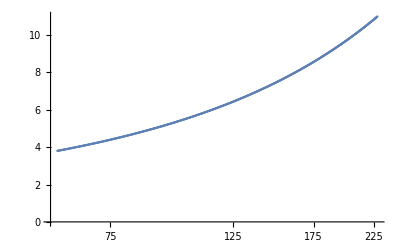

```mathematica
ListLinePlot[Reverse[initboundary,2],ScalingFunctions->{"Log10",None},PlotMarkers->{Automatic,2}]
```

```mathematica
FindPath[NearestNeighborGraph[finepts2],First[finepts2],Last[finepts2]]
```

{}

```mathematica
finepts3=finepts2[[Last[FindShortestTour[finepts2,1,Length[finepts2]]]]];
```

```mathematica
boundary=Reverse[boundaryScaled[[Last[FindShortestTour[boundaryScaled,1,Length[boundaryScaled]]]]],2];
```

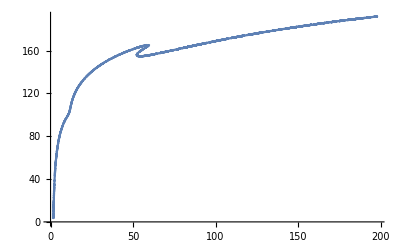

```mathematica
ListPlot[finepts3,Joined->True]
```

```mathematica
{Last[initboundary][[1]],Last[initboundary][[2]]/(2π)}
```

{3.72442,9.26767}

```mathematica
ClearAll["Global`*"];
SetDirectory["D:\\work\\VCSEL experiments\\TeXи\\graphs"];
```

```mathematica
Import["fig[k_a_gd][300 50 4].m"];
```

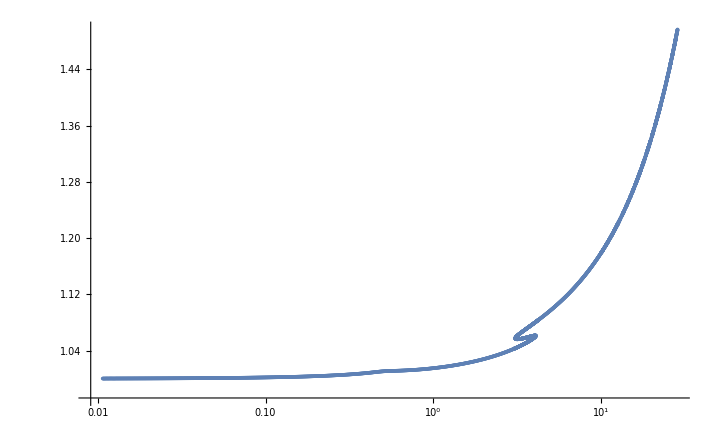

```mathematica
ListPlot[boundary,ScalingFunctions->{"Log10",None}]
```

```mathematica
initpoints={boundaryP1,boundaryP2,boundaryP3}//Flatten[#,1]&;
PointNum3=2000;
accuracy3=10^-7;
sums3=Prepend[Table[Sum[Norm[initpoints[[i]]-initpoints[[i-1]]],{i,2,j}],{j,2,Length[initpoints]}],0];
interp3=Interpolation[Transpose[{sums3,initpoints}],Method->"Spline"];
initfinepts3=Table[interp3[Last[sums3]/(PointNum3)*i],{i,0,PointNum3}];
```

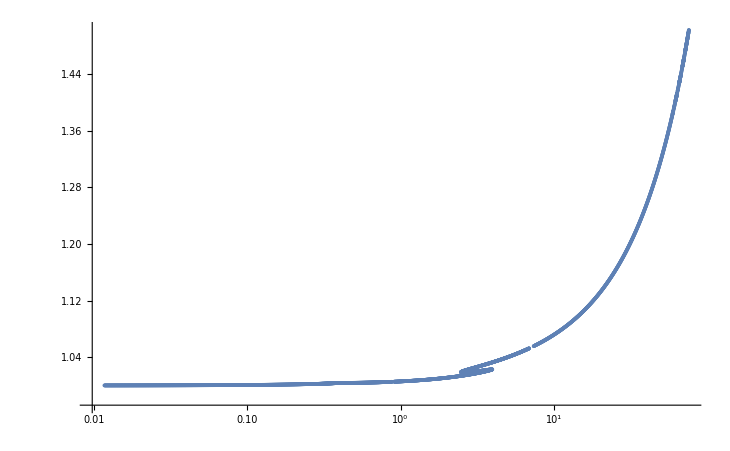

```mathematica
ListPlot[initpoints,ScalingFunctions->{"Log10",None}]
```

```mathematica
finepts2={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts2],i++,
pt=initfinepts2[[i]];
Δxy=initfinepts2[[i+1]]-initfinepts2[[i-1]];
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1//N;
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1//N;
μ=μmin+(μmax-μmin)/Nμ*(pt[[1]]);
γp=γpmin*(γpmax/γpmin)^((pt[[2]])/Nγp);
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 10&&res1==res&&res2==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.03*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.03*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=3,k≤ 10&&res1==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=3,k≤ 10&&res2==res,k++,
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy2,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/Nμ*(ptmid[[1]]);
If[μmid<1,μmid=1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]])/Nγp);
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts2=Append[finepts2,(pt1+pt2)/2];
];
];
```

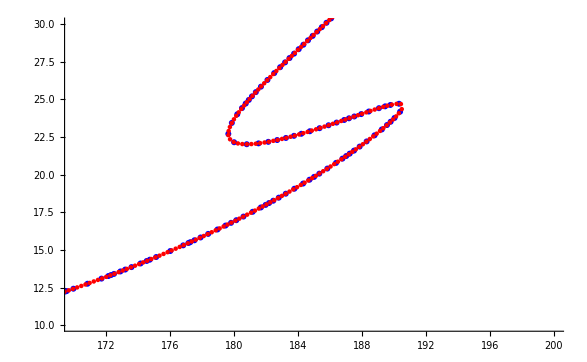

```mathematica
tmpgr1=ListPlot[Reverse[finepts,2],Joined-> False,PlotStyle->Blue];
tmpgr2=ListPlot[Reverse[finepts2,2],Joined-> False,PlotStyle->Red];
Show[tmpgr1,tmpgr2,PlotRange->{{170,200},{10,30}}]
```

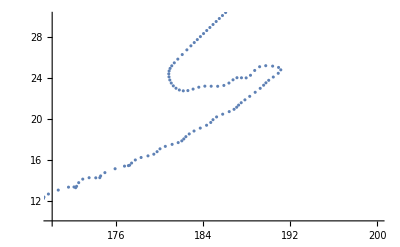

```mathematica
ListPlot[Reverse[initfinepts,2],Joined-> False,PlotRange->{{170,200},{10,30}}]
```

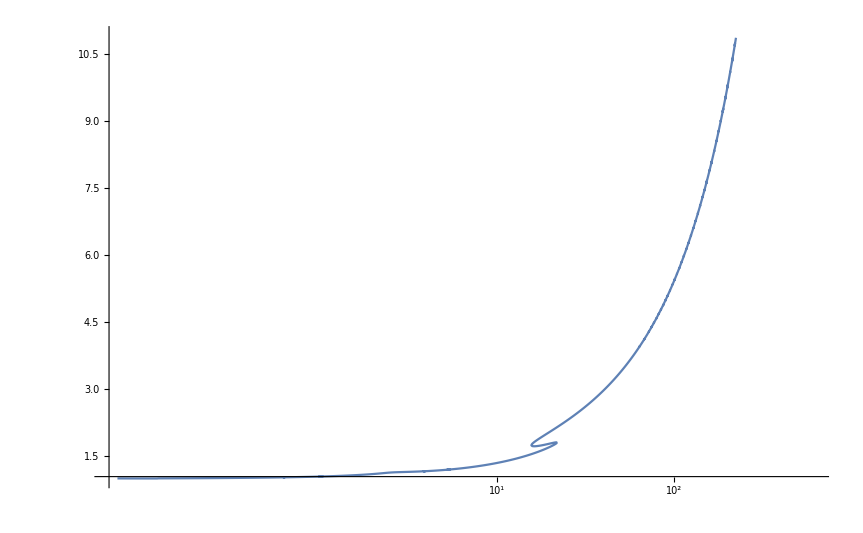

```mathematica
(*Plotting boundary*)
ListPlot[Reverse[boundary,2],Joined-> True,ScalingFunctions->{"Log10",None},PlotRange->{{γpmin,γpmax},{μmin,μmax}}]
```

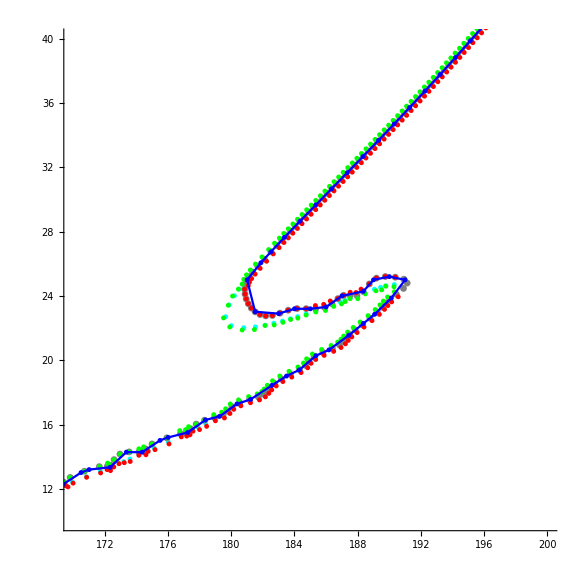

```mathematica
gr1=ListPlot[Reverse[finepts,2],PlotMarkers->{Automatic,5},PlotStyle->Cyan];
gr2=ListPlot[Reverse[initfinepts,2],PlotMarkers->{Automatic,7},PlotStyle->Gray];
p1gr=ListPlot[Reverse[p1s,2],PlotMarkers->{Automatic,5},PlotStyle->Green];
p2gr=ListPlot[Reverse[p2s,2],PlotMarkers->{Automatic,5},PlotStyle->Red];
pt=ListPlot[Reverse[{{49.49141013980161,38.97557295787219},{49.184755339570366,39.10897716181132},{48.89666389409548,39.28266753911388},{48.72596050561139,38.2204349285255},{49.64355017352934,39.997519395097136}},2],PlotMarkers->{Automatic,3},PlotStyle->Red];
Show[gr1,gr2,p1gr,p2gr,grnewpts,PlotRange->{{170,200},{10,40}},ImageSize-> {400,400},AspectRatio->Full]
```

```mathematica
tstpts={{49.49141013980161,38.97557295787219},{49.184755339570366,39.10897716181132},{48.89666389409548,39.28266753911388}};
dxy=tstpts[[3]]-tstpts[[1]];
tst=tstpts[[2]]+{dxy[[2]],-dxy[[1]]}/Sqrt[dxy[[1]]^2+dxy[[2]]^2]//N
tst-tstpts[[2]]
```

{49.6436,39.9975}

{0.458795,0.888542}

```mathematica
{48.72596050561139,38.2204349285255},{49.64355017352934,39.997519395097136}
```

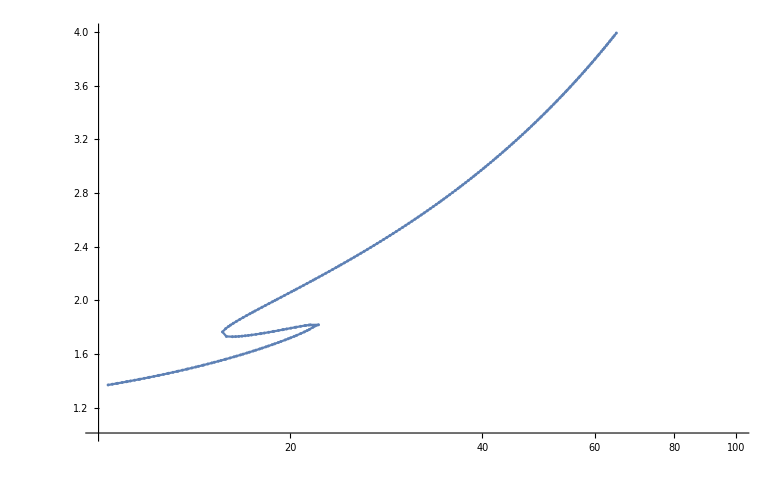

```mathematica
ListPlot[Reverse[boundary,2],Joined-> True,PlotMarkers->{Automatic,3},ScalingFunctions->{"Log10",None},PlotRange->{{γpmin,γpmax},{μmin,μmax}}]
```

```mathematica
listp=ListPlot[Reverse[accuratePoints,2]];
listp1=ListPlot[Reverse[p1s,2],PlotStyle->Blue];
listp2=ListPlot[Reverse[p2s,2],PlotStyle->Red];
Show[ap,lmp,lmpY,listp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

-Graphics-

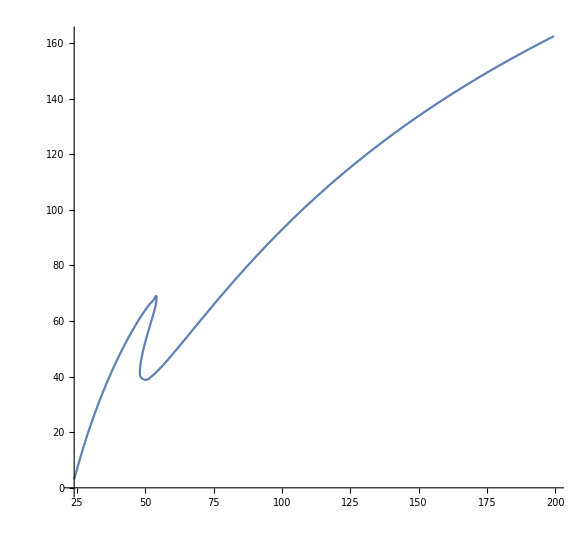

```mathematica
sums=Prepend[Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]],{i,2,j}],{j,2,Length[accuratePoints]}],0];
ParametricPlot[Interpolation[Transpose[{sums,accuratePoints}],Method->"Spline"][t],{t,0,Last[sums]}]
```

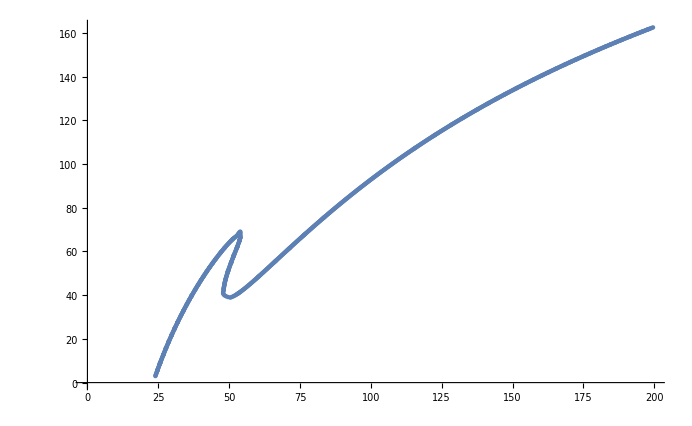

```mathematica
ListPlot[initfinepts]
```

```mathematica
Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]],{i,2,j}],{j,2,Length[accuratePoints]}]
```

{1.38014,2.74721,3.11177,4.56813,5.93245,6.23254,7.27492,8.65768,10.0186,10.4088,11.8315,13.1899,13.5535,14.9995,16.3555,16.7097,18.1619,19.5156,19.8786,21.3191,22.6707,23.0611,24.4715,25.8211,26.2583,27.6193,28.967,29.8652,31.2117,31.6236,33.0062,34.3513,35.2477,36.5919,37.4877,38.8311,39.2238,40.6216,41.9641,42.859,44.201,45.0956,46.4373,47.3318,48.6734,49.5678,50.9096,51.8042,53.1463,54.0412,55.384,56.2795,57.6233,58.5197,60.1153,61.2117,62.1103,63.4599,64.3609,65.8993,67.3314,68.4401,69.3579,70.8807,73.0309,75.5588,76.0375,77.0607,77.36,78.7291,80.1741,80.547,81.9083,83.3089,84.354,84.63,85.9918,87.4838,87.8096,89.1752,90.5984,91.632,91.9148,93.2904,94.7161,95.7375,96.7553,97.7691,98.7786,99.7837,100.785,102.693,105.247,107.149,108.526,109.455,110.737,112.151,113.566,114.982,116.399,117.816,118.974,119.896,121.363,122.782,124.201,125.621,127.041,128.174,129.093,130.591,132.011,133.43,134.85,135.988,136.908,138.398,139.817,141.236,142.655,143.817,144.74,146.2,147.617,149.035,150.452,151.869,153.285,154.453,155.381,156.826,158.241,159.657,161.072,162.487,163.902,165.317,166.732,168.146,169.561,170.975,172.39,173.804,175.218,176.632,178.047,179.461,180.875,182.289,183.704,185.119,186.533,187.948,189.363,190.779,192.194,193.61,195.027,196.443,197.86,199.227,200.151,201.404,202.822,204.24,205.66,207.079,208.439,209.357,210.631,212.052,213.474,214.897,216.225,217.139,218.457,219.882,221.244,222.154,223.448,224.876,226.305,227.611,228.519,229.88,231.311,232.6,233.506,234.894,236.221,237.125,238.483,239.837,240.74,242.079,243.518,244.801,245.702,247.123,248.406,249.306,250.734,252.006,252.906,254.352,255.604,256.502,257.85,258.749,260.157,261.442,262.34,263.795,265.032,265.929,267.274,268.171,269.515,270.412,271.826,273.1,273.996,275.339,276.235,277.693,278.921,279.817,281.159,282.054,283.397,284.292,285.634,286.529,287.871,288.766,290.232,291.45,292.344,293.686,294.58,295.922,296.816,298.158,299.053,300.637}

```mathematica
point=accuratePoints[[1]]-{0.00001,0}
```

{23.974,3.}

```mathematica
μ=μmin+(μmax-μmin)/Nμ*(point[[1]]);
γp=γpmin*(γpmax/γpmin)^((point[[2]])/Nγp);
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

{1,{Qp→0.244943,Qm→0.123096,a→-0.069379}}

```mathematica
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

{0,{Qp→0.647738,Qm→0.041918,a→-0.181763}}

```mathematica
Norm[pt1-pt2]
```

6.

```mathematica
pt1-pt2
```

{2.68328,-5.36656}

```mathematica
i=2;
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
μ=μmin+(μmax-μmin)/Nμ*pt1[[1]]
γp=γpmin*(γpmax/γpmin)^(pt1[[2]]/Nγp)
```

1.65683

10.364

```mathematica
{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N
```

{0.894427,-0.447214}

```mathematica
{μs[[pt[[1]]+1]],γps[[pt[[2]]+1]]}
{μs[[pt[[1]]+2]],γps[[pt[[2]]+2]]}
```

{1.63,10.4713}

{1.66,10.7152}

```mathematica
Image[Reverse[cnt]]
```

-Graphics-

```mathematica
f=ListInterpolation[points,InterpolationOrder->2];

Plot[f[x],{x,0,4}]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,1}.

-Graphics-

```mathematica
Clear[X,Y,p2,L];
X={xm1,0,xp1};
Y={ym1,0,yp1};
L[j_,x_]:=Product[If[i==j,1,(x−X[[i]])/(X[[j]]−X[[i]])],{i,1,3}];
p2[x_]:=Sum[Y[[i]]*L[i,x],{i,1,3}]
```

```mathematica
D[p2[x],x]/.{x-> 0}//FullSimplify
```

(-xp1^2 ym1+xm1^2 yp1)/(xm1 (xm1-xp1) xp1)

```mathematica
p2[x]
```

(x (x-xp1) ym1)/(xm1 (xm1-xp1))+(x (x-xm1) yp1)/(xp1 (-xm1+xp1))

```mathematica
g=Graph[Sort/@{{1,1}<->{1,2},{1,2}<->{3,2},{1,2}<->{1,1},{1,2}<->{1,1},{1,2}<->{2,3},{3,2}<->{3,3},{3,3}<->{2,3},{2,3}<->{3,4}}//DeleteDuplicates,PlotTheme->"IndexLabeled"]
```

-Graphics-

```mathematica
FindHamiltonianPath[g]
```

{{3,4},{2,3},{3,3},{3,2},{1,2},{1,1}}

```mathematica
HighlightGraph[g,PathGraph[%]]
```

-Graphics-

```mathematica
ArrayMesh[cnt]
```

### Plotting by pixels v2

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];

p=-CoefficientList[CharacteristicPolynomial[(tmp3/.{Λ-> μ}/.Nsol),λ],λ];

If[AllTrue[p,Positive],
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)

If[AllTrue[Dets,Positive],
result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] 
,
result[[i,j]]=0
],
If[oldresult[[i,j]]>0,Print[i," ",j],]
]
]];
Image[Reverse[result]]
```

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

General::stop: Further output of CharacteristicPolynomial::inf will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.107997,0.906551,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.123634,0.910422,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.139076,0.914214,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

-Graphics-

```mathematica
Image[Reverse[oldresult-result]]
Image[Reverse[oldresult]]
```

-Graphics-

-Graphics-

```mathematica
μ=μs[[100]];
γp=γps[[83]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];
p=charpolycoefs/.Nsol;
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
```

```mathematica
p
```

{1.02348×10^10,1.18555×10^8,-1.30236×10^6,35269.8,121.689}